# Drell-Yan in Wandzura-Wilczek-type approximation. Results of the paper: “Drell-Yan in Wandzura-Wilczek-type approximation” S. Bastami, L. Gamberg, B. Pasquini, A. Prokudin, P. Schweitzer author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/DY/mathematica

## Constants

```mathematica
Mproton = 0.938;
Mpion = 0.135;
```

## Collinear functions

## Read and interpolate DSS collinear fragmentation functions.

```mathematica
DSShplus= ReadList["./Grids/fragmentationpiplus.dat",Real,RecordLists-> True];
DSShminus= ReadList["./Grids/fragmentationpiminus.dat",Real,RecordLists-> True];
```

```mathematica
uhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,3]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}]
dhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,4]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
shplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,5]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
ubhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,6]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
dbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,7]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
sbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,8]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[…]

```mathematica
uhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,3]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}]
dhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,4]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
shminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,5]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
ubhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,6]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
dbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,7]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
sbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,8]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[…]

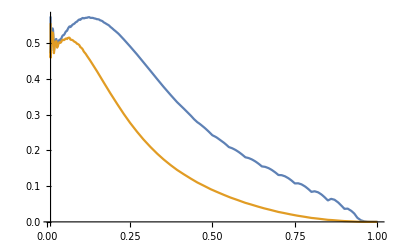

```mathematica
Plot[{z uhplus[z,3.],z dhplus[z,3.]},{z,0.01,1}]
```

## Read and interpolate MSTW collinear distribution functions.

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
?ReadPDFGrid
```

The function ReadPDFGrid[prefix,ih] reads the PDF grid corresponding to eigenvector set ih, where ih=0 is the central set, into memory from the location specified by prefix.

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f (apart from the gluon has f=0, not 21), that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

```mathematica
Use of the central PDF set
```

central of PDF set the Use

```mathematica
prefix="Grids/mstw2008lo";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from Grids/mstw2008lo.00.dat

{5.43933,Null}

```mathematica
Clear[upv,dnv,usea,dsea,str,sbar];
```

```mathematica
upv[x_,Q2_]:=xf[0,x,Sqrt[Q2],8]/x
dnv[x_,Q2_]:=xf[0,x,Sqrt[Q2],7]/x
usea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-2]/x
dsea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-1]/x
str[x_,Q2_]:=xf[0,x,Sqrt[Q2],3]/x
sbar[x_,Q2_]:=xf[0,x,Sqrt[Q2],-3]/x
up[x_,Q2_]:=upv[x,Sqrt[Q2]]+usea[x,Sqrt[Q2]]
dn[x_,Q2_]:=dnv[x,Sqrt[Q2]]+dsea[x,Sqrt[Q2]]
upbar[x_,Q2_]:=usea[x,Sqrt[Q2]]
dnbar[x_,Q2_]:=dsea[x,Sqrt[Q2]]
```

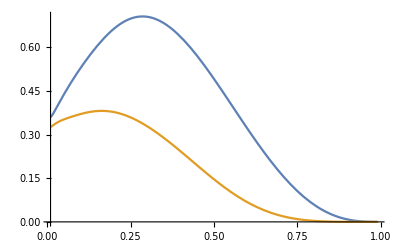

```mathematica
Plot[{x up[x,1.],x dn[x,1.]},{x,0.01,0.99}]
```

## Read and interpolate helicity collinear distribution functions. Gluck:1998xa

```mathematica
g1param= ReadList["./Grids/g1.dat",Real,RecordLists-> True];
```

```mathematica
g1u=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,3]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1d=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,4]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1s=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,5]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1ubar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,6]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1dbar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,7]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1sbar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,8]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
```

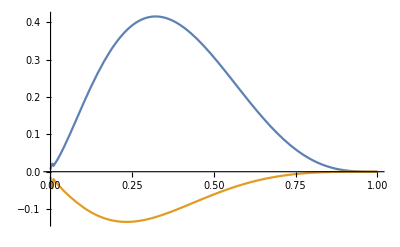

```mathematica
Plot[{x*g1u[x,1.],x*g1d[x,1.]},{x,0.001,1}]
```

## Read and interpolate pion collinear distribution functions.

```mathematica
pion= ReadList["./Grids/pion_mrss.dat",Real,RecordLists-> True];
```

```mathematica
pionu=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,3]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
piond=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,4]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pions=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,5]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pionubar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,6]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
piondbar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,7]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pionsbar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,8]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
```

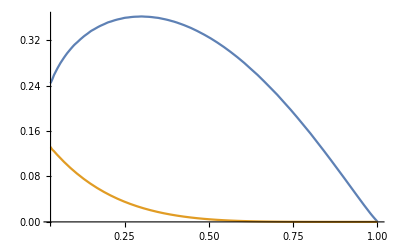

```mathematica
Plot[{x*pionu[x,1.],x*piond[x,1.]},{x,0.03,1}]
```

Pi - functions :

```mathematica
piminusu=piond;
piminusd = pionu;
piminuss = pions;
piminusubar =piondbar;
piminusdbar =pionubar;
piminussbar =pionsbar;
```

## Read and interpolate Soffer Bound collinear distribution functions.

```mathematica
sb= ReadList["./Grids/SofferBound.dat",Real,RecordLists-> True];
```

```mathematica
sb1u=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,3]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1d=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,4]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1s=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,5]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1ubar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,6]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1dbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,7]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1sbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,8]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
```

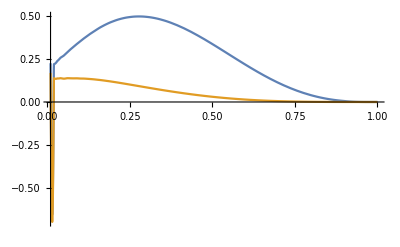

```mathematica
Plot[{x*sb1u[x,1.],x*sb1d[x,1.]},{x,0.01,1}]
```

## 6 “basis” functions for the proton f_1, h_1, g_1, f_(1T)^⊥,h_(1T)^⊥, h_1^⊥

## f_1

```mathematica
(*2005 fit Appendix A.1 [hep-ph/0501196]*)
Clear[avk];
avk=0.25;
(* distribution*)


f1u[x_,Q2_ ]:= up[x,Q2];
f1d[x_,Q2_ ]:= dn[x,Q2] ;
f1ubar[x_,Q2_ ]:= upbar[x,Q2];  
f1dbar[x_,Q2_ ]:= dnbar[x,Q2] ; 
f1s[x_,Q2_ ]:= str[x,Q2];
f1sbar[x_,Q2_ ]:= sbar[x,Q2];


f1uTMD[x_,Q2_ ,kt_]:= up[x,Q2]1/(π avk) Exp[-kt^2/avk];
f1dTMD[x_,Q2_,kt_ ]:= dn[x,Q2] 1/(π avk) Exp[-kt^2/avk];
f1ubarTMD[x_,Q2_,kt_ ]:= upbar[x,Q2]  1/(π avk) Exp[-kt^2/avk];
f1dbarTMD[x_,Q2_ ,kt_]:= dnbar[x,Q2]  1/(π avk) Exp[-kt^2/avk];
f1sTMD[x_,Q2_,kt_ ]:= str[x,Q2]1/(π avk) Exp[-kt^2/avk];
f1sbarTMD[x_,Q2_,kt_ ]:= sbar[x,Q2]1/(π avk) Exp[-kt^2/avk];
```

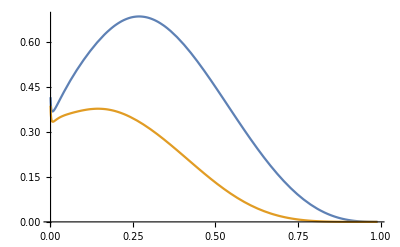

```mathematica
Plot[{x f1u[x,1.7], x f1d[x,1.7]},{x,0.001,0.99}]
```

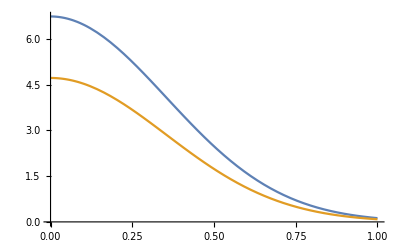

```mathematica
Plot[{f1uTMD[0.1,1.,kt],f1dTMD[0.1,1.,kt]},{kt,0,1}]
```

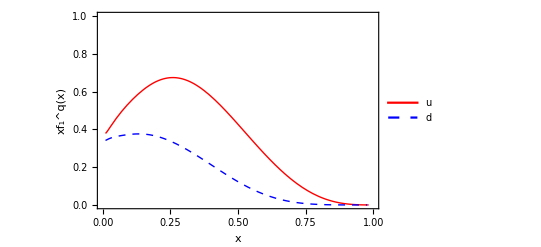

```mathematica
f1plot =Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1.pdf",%,Background->None]
```

../tex/figs/f1.pdf

```mathematica
ExpandFileName["../tex/figs/f1.pdf"]
```

/Users/avp5627/GIT/DY/tex/figs/f1.pdf

## h_1

```mathematica
(*2013 fit Appendix A.4 [1303.3822].*)
Clear[NuT,NdT,alphaT,betaT];
NuT=0.46;
NdT=-1.000;
alphaT=1.11;
betaT=3.64;

(* Transversity function with DGLAP Evolution*)
h1u[x_,Q2_]:=(NuT x^alphaT (1-x)^betaT(alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT))) sb1u[x,Q2];
h1d[x_,Q2_]:=(NdT x^alphaT (1-x)^betaT (alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT)))sb1d[x,Q2];

h1uTMD[x_,Q2_,kt_]:=h1u[x,Q2]1/(π avk) Exp[-kt^2/avk];
h1dTMD[x_,Q2_,kt_]:=h1d[x,Q2]1/(π avk) Exp[-kt^2/avk];


year = 2013;
width = 25;
MyLabel= StringForm["`` fit ⟨k_⊥^2⟩ = 0.`` (GeV^2).",year,width]
```

2013 fit ⟨k_⊥^2⟩ = 0.25 (GeV^2).

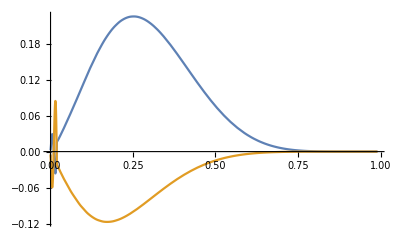

```mathematica
Plot[{x h1u[x,1.], x h1d[x,1.]},{x,0.001,0.99}]
```

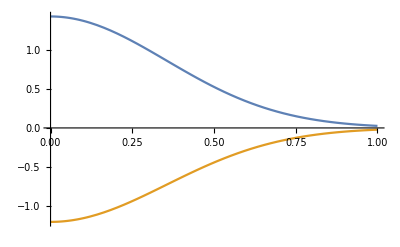

```mathematica
Plot[{h1uTMD[0.1,1.,kt],h1dTMD[0.1,1.,kt]},{kt,0,1}]
```

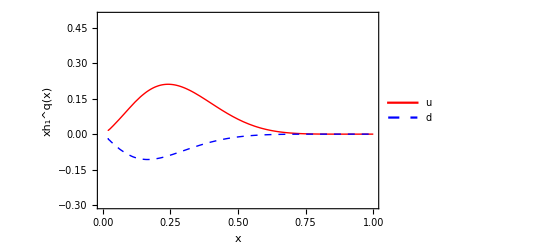

```mathematica
h1plot =Plot[{x h1u[x,2.4],x h1d[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1.pdf",%,Background->None]
```

../tex/figs/h1.pdf

## g_1

```mathematica
(*Lattice fit Appendix A. 2 [0908.1283].*)
Clear[avkg];
avkg=avk 0.76 ;
 

(* Helicity functions with DGLAP Evolution*)


g1uTMD[x_,Q2_,kt_]:=g1u[x,Q2]1/(π avkg) Exp[-kt^2/avkg];
g1dTMD[x_,Q2_,kt_]:=g1d[x,Q2]1/(π avkg) Exp[-kt^2/avkg];
```

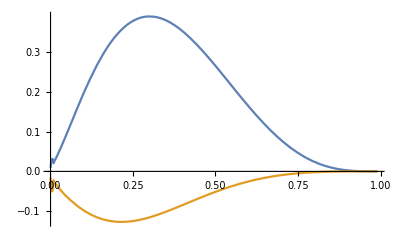

```mathematica
Plot[{x g1u[x,1.7], x g1d[x,1.7]},{x,0.001,0.99}]
```

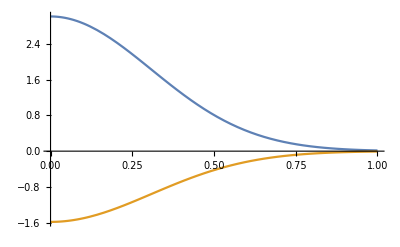

```mathematica
Plot[{g1uTMD[0.1,1.,kt],g1dTMD[0.1,1.,kt]},{kt,0,1}]
```

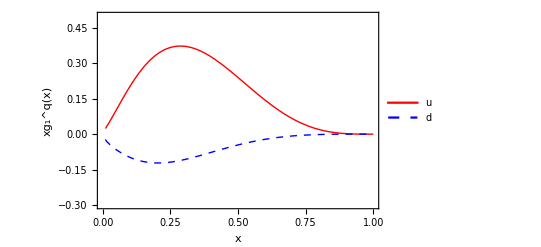

```mathematica
g1plot =Plot[{x g1u[x,2.4],x g1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xg_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/g1.pdf",%,Background->None]
```

../tex/figs/g1.pdf

## f_(1T)^⊥ Drell-Yan

```mathematica
(*2011 fit Appendix A. 3 1107.4446.*)
Clear[Ms,avks,Nu,Nusea,Nd,Ndsea,Nst,Nstbar,alphauv,alphadv,asea,beta, Mp];
Ms=Sqrt[0.19];
avks=avk Ms^2/(avk +Ms^2);
Nu=0.4;
Nd=-0.97;
alphauv=0.35;
alphadv=0.44;
betauv=2.6;
betadv=0.9;
avPTs[z_]:= Sqrt[avp^2+avks^2 z^2]
Mp=0.938;

(* Sivers SIDIS*)
usiv[x_,Q2_]:=(Nu x^alphauv (1-x)^betauv (alphauv+ betauv)^(alphauv+ betauv)/((alphauv^alphauv)( betauv^betauv))) up[x,Q2]
dsiv[x_,Q2_]:=(Nd x^alphadv (1-x)^betadv (alphadv+ betadv)^(alphadv+ betadv)/((alphadv^alphadv)( betadv^betadv)))dn[x,Q2]
ubarsiv[x_,Q2_]:=0.
dbarsiv[x_,Q2_]:=0.
ssiv[x_,Q2_]:=0.
sbarsiv[x_,Q2_]:=0.

 (* Sivers SIDIS *)
f1TperpuFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)usiv[x,Q2] avks^2/avk ;
f1TperpdFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)dsiv[x,Q2] avks^2/avk;
f1TperpubarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)ubarsiv[x,Q2] avks^2/avk ;
f1TperpdbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)dbarsiv[x,Q2] avks^2/avk;
f1TperpsFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)ssiv[x,Q2] avks^2/avk ;
f1TperpsbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)sbarsiv[x,Q2] avks^2/avk;


f1TperpuTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)usiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpdTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpubarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ubarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpdbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dbarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpsTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ssiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpsbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)sbarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];

(* Sivers in Drell Yan should change sign by factor (-1)  *)


f1TperpuFirstMoment[x_,Q2_]=(-1) f1TperpuFirstMoment[x,Q2];
f1TperpdFirstMoment[x_,Q2_]=(-1) f1TperpdFirstMoment[x,Q2];
f1TperpubarFirstMoment[x_,Q2_]=(-1) f1TperpubarFirstMoment[x,Q2] ;
f1TperpdbarFirstMoment[x_,Q2_]=(-1) f1TperpdbarFirstMoment[x,Q2];
f1TperpsFirstMoment[x_,Q2_]=(-1) f1TperpsFirstMoment[x,Q2] ;
f1TperpsbarFirstMoment[x_,Q2_]= (-1) f1TperpsbarFirstMoment[x,Q2];


f1TperpuTMD[x_,Q2_,kt_]= (-1) f1TperpuTMD[x,Q2,kt];
f1TperpdTMD[x_,Q2_,kt_]=(-1) f1TperpdTMD[x,Q2,kt];
f1TperpubarTMD[x_,Q2_,kt_]=(-1) h1perpubarTMD[x,Q2,kt];
f1TperpdbarTMD[x_,Q2_,kt_]=(-1) f1TperpdbarTMD[x,Q2,kt];
f1TperpsTMD[x_,Q2_,kt_]=(-1) f1TperpsTMD[x,Q2,kt];
f1TperpsbarTMD[x_,Q2_,kt_]=(-1) f1TperpsbarTMD[x,Q2,kt];
```

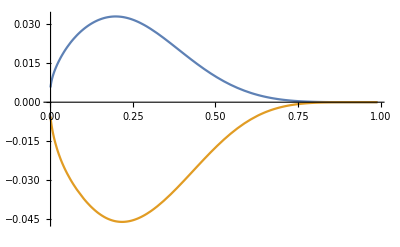

```mathematica
Plot[{x f1TperpuFirstMoment[x,1.],x f1TperpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

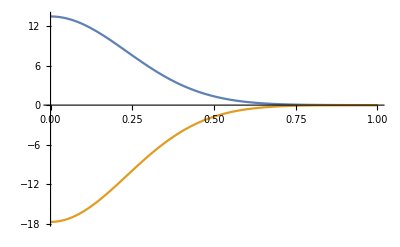

```mathematica
Plot[{f1TperpuTMD[0.1,1.,kt],f1TperpdTMD[0.1,1.,kt]},{kt,0,1}]
```

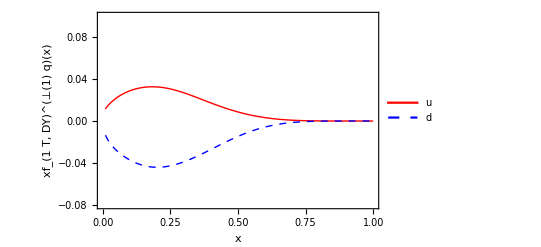

```mathematica
f1Tperpplot =Plot[{x f1TperpuFirstMoment[x,2.4],x f1TperpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.08,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_(1  T,  DY)^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1Tperp.pdf",%,Background->None]
```

../tex/figs/f1Tperp.pdf

## h_(1T)^⊥

```mathematica
(* 2015 fit Appendix A. 6 [1411.0580]. *)
Clear[MTT,avkTT,NuTT,NdTT,alphaTT,betaTT];
MTT=Sqrt[0.18];
avkTT=avk MTT^2/(avk+MTT^2);
NuTT=1;
NdTT=-1;
alphaTT=2.5;
betaTT=2.;
(* Pretzelosity function with DGLAP Evolution *)
huTT[x_,Q2_]:=ⅇ(NuTT x^alphaTT (1-x)^betaTT (alphaTT+ betaTT)^(alphaTT+ betaTT)/((alphaTT^alphaTT)( betaTT^betaTT))) (up[x,Q2]-g1u[x,Q2])
hdTT[x_,Q2_]:=ⅇ(NdTT x^alphaTT(1-x)^betaTT (alphaTT+ betaTT)^(alphaTT+ betaTT)/((alphaTT^alphaTT)( betaTT^betaTT)))(dn[x,Q2]-g1d[x,Q2])


 (* Pretzelosity function with DGLAP Evolution *)
h1TperpuFirstMoment[x_,Q2_]:=1/(2 MTT^2)huTT[x,Q2] avkTT^2/avk ;
h1TperpdFirstMoment[x_,Q2_]:=1/(2 MTT^2)hdTT[x,Q2] avkTT^2/avk;



h1TperpuTMD[x_,Q2_,kt_]:=Mp^2/MTT^2  huTT[x,Q2]1/(π avk) Exp[-kt^2/avkTT];
h1TperpdTMD[x_,Q2_,kt_]:=Mp^2/MTT^2  hdTT[x,Q2]1/(π avk) Exp[-kt^2/avkTT];


h1TperpuSecondMoment[x_,Q2_]:=1/(2 Mp^2 MTT^2)huTT[x,Q2] avkTT^3/avk ;
h1TperpdSecondMoment[x_,Q2_]:=1/(2 Mp^2 MTT^2)hdTT[x,Q2] avkTT^3/avk;
```

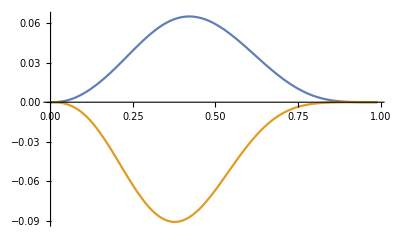

```mathematica
Plot[{x h1TperpuFirstMoment[x,1.],x h1TperpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

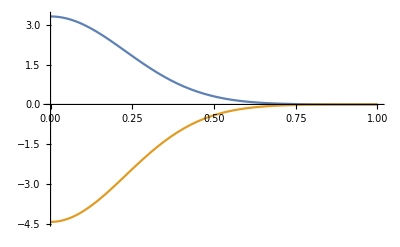

```mathematica
Plot[{h1TperpuTMD[0.1,1.,kt],h1TperpdTMD[0.1,1.,kt]},{kt,0,1}]
```

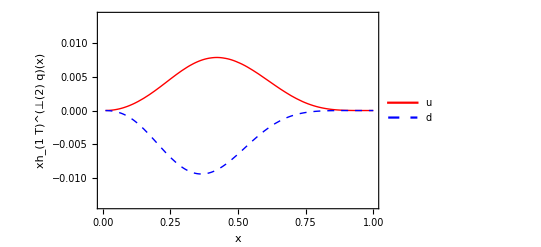

```mathematica
h1Tperpplot =Plot[{x h1TperpuSecondMoment[x,2.4],x h1TperpdSecondMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.014,0.014}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_(1  T)^(⊥(2) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.8,0.75}]]
```

```mathematica
Export["../tex/figs/h1Tperp.pdf",%,Background->None]
```

../tex/figs/h1Tperp.pdf

## h_1^⊥ Drell-Yan

```mathematica
(* 2010 fit Barone et al Appendix A. 5 [0912.5194]. https://arxiv.org/pdf/0912.5194.pdf *)
MsBM=Sqrt[0.34];
avksBM=avk Ms^2/(avk +Ms^2);
avkBM =avksBM;
NuBM=2.1*0.35;
NuseaBM=-1.*0.04;
NdBM=(-1.111)*(-0.9000);
NdseaBM=-1.*0.4;
NstBM=0;
NstbarBM=0;
alphauvBM=0.73;
alphadvBM=1.08;
aseaBM=0.79;
betaBM=3.46;
avPTsBM[z_]:= Sqrt[avp^2+avksBM^2 z^2] 



 (* Boer-Mulders function with DGLAP Evolution *)
usivBM[x_,Q2_]:=(NuBM x^alphauvBM (1-x)^betaBM (alphauvBM+ betaBM)^(alphauvBM+ betaBM)/((alphauvBM^alphauvBM)( betaBM^betaBM))) up[x,Q2]
dsivBM[x_,Q2_]:=(NdBM x^alphadvBM (1-x)^betaBM (alphadvBM+ betaBM)^(alphadvBM+ betaBM)/((alphadvBM^alphadvBM)( betaBM^betaBM)))dn[x,Q2]
ubarsivBM[x_,Q2_]:=(NuseaBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) upbar[x,Q2]
dbarsivBM[x_,Q2_]:=(NdseaBM x^aseaBM (1-x)^betaBM(aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) dnbar[x,Q2]
ssivBM[x_,Q2_]:=(NstBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) str[x,Q2]
sbarsivBM[x_,Q2_]:=(NstbarBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) sbar[x,Q2]

 (* BM SIDIS *)
h1perpuFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)usivBM[x,Q2] avksBM^2/avk ;
h1perpdFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)dsivBM[x,Q2] avksBM^2/avk;
h1perpubarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)ubarsivBM[x,Q2] avksBM^2/avk ;
h1perpdbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)dbarsivBM[x,Q2] avksBM^2/avk;
h1perpsFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)ssivBM[x,Q2] avksBM^2/avk ;
h1perpsbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)sbarsivBM[x,Q2] avksBM^2/avk;

(* BM SIDIS *)
h1perpuTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)usivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpdTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpubarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ubarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpdbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dbarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpsTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ssivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpsbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)sbarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
(* BM Drell Yan should change sign by factor (-1)  *)

h1perpuFirstMoment[x_,Q2_]=(-1) h1perpuFirstMoment[x,Q2];
h1perpdFirstMoment[x_,Q2_]=(-1) h1perpdFirstMoment[x,Q2];
h1perpubarFirstMoment[x_,Q2_]=(-1) h1perpubarFirstMoment[x,Q2] ;
h1perpdbarFirstMoment[x_,Q2_]=(-1) h1perpdbarFirstMoment[x,Q2];
h1perpsFirstMoment[x_,Q2_]=(-1) h1perpsFirstMoment[x,Q2] ;
h1perpsbarFirstMoment[x_,Q2_]= (-1) h1perpsbarFirstMoment[x,Q2];


h1perpuTMD[x_,Q2_,kt_]= (-1) h1perpuTMD[x,Q2,kt];
h1perpdTMD[x_,Q2_,kt_]=(-1) h1perpdTMD[x,Q2,kt];
h1perpubarTMD[x_,Q2_,kt_]=(-1) h1perpubarTMD[x,Q2,kt];
h1perpdbarTMD[x_,Q2_,kt_]=(-1) h1perpdbarTMD[x,Q2,kt];
h1perpsTMD[x_,Q2_,kt_]=(-1) h1perpsTMD[x,Q2,kt];
h1perpsbarTMD[x_,Q2_,kt_]=(-1) h1perpsbTMD[x,Q2,kt];
```

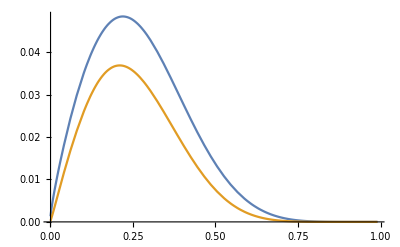

```mathematica
Plot[{x h1perpuFirstMoment[x,1.],x h1perpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

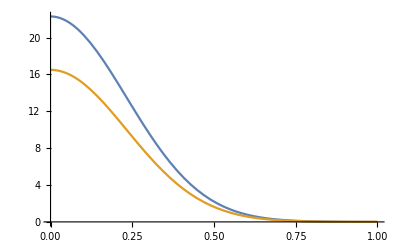

```mathematica
Plot[{h1perpuTMD[0.1,1.,kt],h1perpdTMD[0.1,1.,kt]},{kt,0,1}]
```

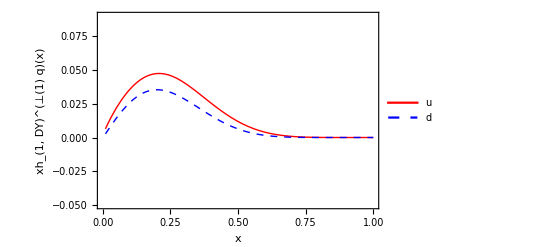

```mathematica
h1perpplot =Plot[{x h1perpuFirstMoment[x,2.4],x h1perpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.09}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_(1,  DY)^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.17}]]
```

```mathematica
Export["../tex/figs/h1perpBM.pdf",%,Background->None]
```

../tex/figs/h1perpBM.pdf

## 2 “basis” functions for the pion f_1, h_1^⊥

## f_1 pion-

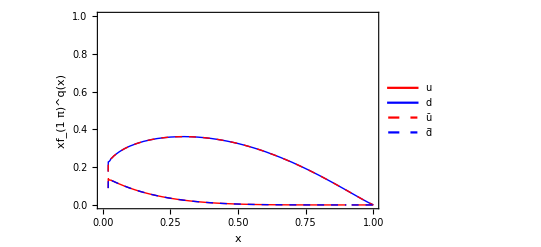

```mathematica
f1plot =Plot[{x piminusu[x,2.4],x piminusd[x,2.4],x piminusubar[x,2.4],x piminusdbar[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_(1  π)^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1pion.pdf",%,Background->None]
```

../tex/figs/f1pion.pdf

## f_1 Pion Read and interpolate pion- (ubar,d) Barbara

```mathematica
barbara= ReadList["./Grids/x_f1_ubar_lo_q2_25p0_pion_alexey.dat",Real,RecordLists-> True];
```

```mathematica
bubar=Interpolation[Table[{barbara[[i,1]],barbara[[i,2]]},{i,1,Length[barbara]}]];
```

```mathematica
barbara= ReadList["./Grids/x_f1_up_lo_q2_25p0_pion_alexey.dat",Real,RecordLists-> True];
```

```mathematica
bu=Interpolation[Table[{barbara[[i,1]],barbara[[i,2]]},{i,1,Length[barbara]}]];
```

```mathematica
piminusu[x_,Q2_]=bu[x]/x;
piminusd[x_,Q2_] = bubar[x]/x;
piminuss[x_,Q2_] = bu[x]/x;
piminusubar[x_,Q2_] =bubar[x]/x;
piminusdbar[x_,Q2_] =bu[x]/x;
piminussbar[x_,Q2_] =bu[x]/x;
```

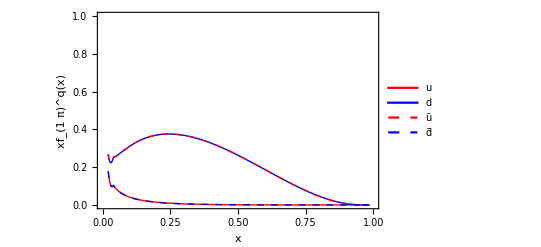

```mathematica
f1plot =Plot[{x piminusu[x,2.4],x piminusd[x,2.4],x piminusubar[x,2.4],x piminusdbar[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_(1  π)^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1pionBarbara.pdf",%,Background->None]
```

../tex/figs/f1pionBarbara.pdf

## h_1^⊥ Pion Read and interpolate pion Boer Mulders first moment

```mathematica
bmgamberg= ReadList["./Grids/bmgamberg.dat",Real,RecordLists-> True];
```

```mathematica
bmpion=Interpolation[Table[{bmgamberg[[i,1]],bmgamberg[[i,2]]},{i,1,Length[bmgamberg]}]];
```

```mathematica
(* BM Drell Yan should change sign by factor (-1)  *)
BoerMuldersPionFirstMoment[x_,Q2_] := -bmpion[x]/(x*Mpion^2);
```

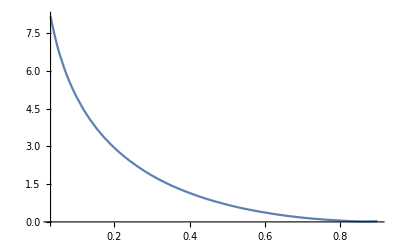

```mathematica
Plot[{BoerMuldersPionFirstMoment[x,2.4]},{x,0.03,0.9}]
```

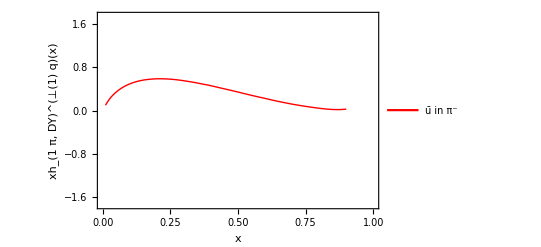

```mathematica
h1perpplotPion =Plot[{x BoerMuldersPionFirstMoment[x, 4]},{x,0.01,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-1.75,1.75}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_(1  π,  DY)^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"ū in π^-"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1perpBMpion.pdf",%,Background->None]
```

../tex/figs/h1perpBMpion.pdf

## h_1^⊥ Pion Read and interpolate pion Boer Mulders first moment Barbara

```mathematica
barbara= ReadList["./Grids/x_first_moment_bm_up_lo_q2_25p0_pion_alexey.dat",Real,RecordLists-> True];
```

```mathematica
bmpion=Interpolation[Table[{barbara[[i,1]],barbara[[i,2]]},{i,1,Length[barbara]}]];
```

```mathematica
(* BM Drell Yan should change sign by factor (-1)  *)
BoerMuldersPionFirstMoment[x_,Q2_] := -bmpion[x]/(x);
```

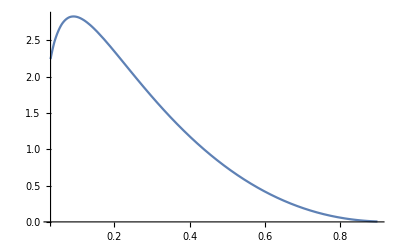

```mathematica
Plot[{BoerMuldersPionFirstMoment[x,2.4]},{x,0.03,0.9}]
```

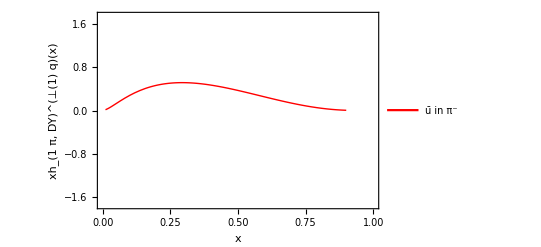

```mathematica
h1perpplotPion =Plot[{x BoerMuldersPionFirstMoment[x, 4]},{x,0.01,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-1.75,1.75}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_(1  π,  DY)^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"ū in π^-"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1perpBMpion.pdf",%,Background->None]
```

../tex/figs/h1perpBMpion.pdf

## WW-type relations

## WW-type relation for h_(1L)^⊥

```mathematica
(*Eq. 3.6 (b)*)
h1Lu[x_,Q_] :=-x^2 NIntegrate[h1u[y,Q]/y^2,{y,x,1.}];
h1Ld[x_,Q_] :=-x^2  NIntegrate[h1d[y,Q]/y^2,{y,x,1.}];
```

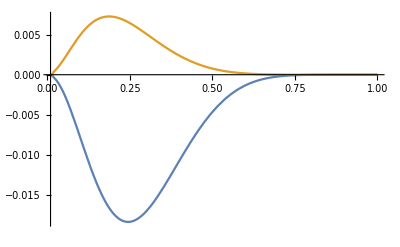

```mathematica
Plot[{x h1Lu[x,1.],x h1Ld[x,1.]},{x,0.01,1}]
```

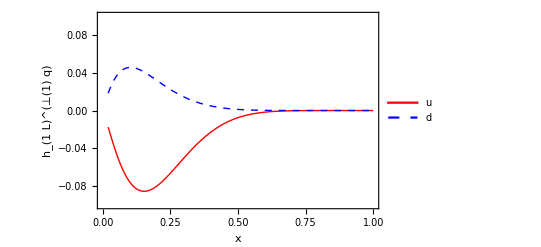

```mathematica
Plot[{h1Lu[x,2.4],h1Ld[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","h_(1  L)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1Lperp.pdf",%,Background->None]
```

../tex/figs/h1Lperp.pdf

## WW relation for g_T

```mathematica
(*Eq. 3.2 (a)*)
gTu[x_,Q2_] := NIntegrate[g1u[y,Q2]/y,{y,x,1.}];
gTd[x_,Q2_] := NIntegrate[g1d[y,Q2]/y,{y,x,1.}];
gTubar[x_,Q2_] := NIntegrate[g1ubar[y,Q2]/y,{y,x,1.}];
gTdbar[x_,Q2_] := NIntegrate[g1dbar[y,Q2]/y,{y,x,1.}];
gTs[x_,Q2_] := NIntegrate[g1s[y,Q2]/y,{y,x,1.}];
gTsbar[x_,Q2_] := NIntegrate[g1sbar[y,Q2]/y,{y,x,1.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained 6.16095 and 0.0000104912 for the integral and error estimates.

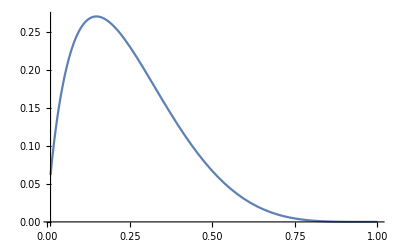

```mathematica
Plot[{x*gTu[x,1.]},{x,0.01,1}]
```

## WW-type relation for g_(1T)^⊥

```mathematica
(*Eq. 3.6 (a)*)
g1Tperpu[x_,Q2_] := x NIntegrate[g1u[y,Q2]/y,{y,x,1.}];
g1Tperpd[x_,Q2_] := x NIntegrate[g1d[y,Q2]/y,{y,x,1.}];
g1Tperpubar[x_,Q2_] := x NIntegrate[g1ubar[y,Q2]/y,{y,x,1.}];
g1Tperpdbar[x_,Q2_] := x NIntegrate[g1dbar[y,Q2]/y,{y,x,1.}];
g1Tperps[x_,Q2_] := x NIntegrate[g1s[y,Q2]/y,{y,x,1.}];
g1Tperpsbar[x_,Q2_] := x NIntegrate[g1sbar[y,Q2]/y,{y,x,1.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained 7.32788 and 0.0000320626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained -4.60653 and 0.0000401872 for the integral and error estimates.

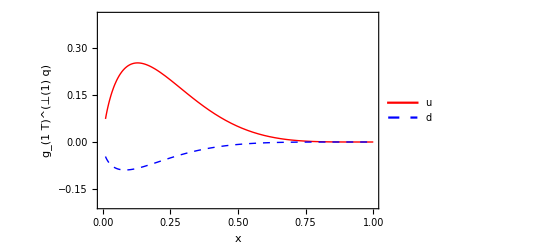

```mathematica
Plot[{g1Tperpu[x,2.4],g1Tperpd[x,2.4](*,g1Tperpubar[x,2.4],g1Tperpdbar[x,2.4]*)},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.2,0.4}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"(*,"ū","d̄"*)},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/g1t.pdf",%,Background->None]
```

../tex/figs/g1t.pdf

## Asymmetries Drell-Yan analytical calculation of all terms in DY cross section using “Dilepton production from polarized hadron hadron collisions” S. Arnold, A. Metz, M. Schlegel https://arxiv.org/abs/0809.2262v2

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[qT]:=Subscript[q, T];
Format[kta]:=Subscript[k, aT];
Format[ktb]:=Subscript[k, bT];
Format[f1a]:=Subscript[f, 1a];
Format[f1b]:=Subscript[f, 1b];
Format[avkta]:=Subscript[k, aTA]^2;
Format[avktb]:=Subscript[k, bTA]^2;

Format[hh1a]:=Subscript[h, 1a];
Format[hh1b]:=Subscript[h, 1b];
Format[ktah1]:=Subscript[k, aTh1]^2;
Format[ktbh1]:=Subscript[k, bTh1]^2;

Format[h1perpFirstMomenta] := Subscript[h, 1a]^(perp FIRST);
Format[h1perpFirstMomentb] := Subscript[h, 1b]^(perp FIRST);
Format[ktaBM]:=Subscript[k, aTBOERMULDERS]^2;
Format[ktbBM]:=Subscript[k, bTBOERMULDERS]^2;

Format[f1TperpFirstMomenta] := Subscript[f, 1Ta]^(perp FIRST);
Format[f1TperpFirstMomentb] := Subscript[f, 1Tb]^(perp FIRST);
Format[ktaS]:=Subscript[k, aTSIVERS]^2;
Format[ktbS]:=Subscript[k, bTSIVERS]^2;

Format[h1TperpSecondMomenta] := Subscript[h, 1Ta]^(perp SECOND);
Format[h1TperpSecondMomentb] := Subscript[h, 1Tb]^(perp SECOND);
Format[ktaP]:=Subscript[k, aTPRETZELOSITY]^2;
Format[ktbP]:=Subscript[k, bTPRETZELOSITY]^2;


$Assumptions={avkta>0,avktb>0,qT>0, ktah1>0,ktbh1>0, ktaBM >0, ktbBM >0,ktaS>0,ktbS>0,ktaP>0,ktbP>0} ;
```

#### Moments :

k_T and p_Tmoments in Piet' s definition are

f_1^(n)(x) = ∫(k_T^2/(2 M^2))^n f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)(k_T^2/(2 M^2))^n k_T ⅆ k_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
XMomentTMD[n_,func_]:=∫_0^∞ ∫_0^(2 π) kt (kt^2/(2 M^2))^n func[kt^2]ⅆphiⅆkt
```

#### Convolution is defined as C[wf_1f_2] = 1/N_c ∑_q e_q^2∫ⅆ^2 k_aTⅆ^2 k_bT δ^(2)(q_T-k_aT-k_bT)w(k_aT,k_bT)f_1^a(x_a,k_aT^2)f_2^a(x_b,k_bT^2), q=q,q̄

```mathematica
ConvolutionTMD[weight_,f1_,f2_]:=∫_0^∞ ∫_0^(2 π) kta weight[kta,qT,phi] f1[kta^2]f2[kta kta+ qT qT - 2 kta qT Cos[phi]]ⅆphiⅆkta
qTConvolutionTMD[qTweight_,weight_,f1_,f2_]:= ∫_0^∞ ∫_0^(2 π) qT qTweight[qT] ConvolutionTMD[weight,f1,f2] ⅆphiⅆqT
```

#### Distributions and fragmentation function:

```mathematica
f1a[kt2_] := f1a 1/(π avkta) Exp[-kt2/avkta]; (* unpolarised distribution in A *)
f1b[kt2_] := f1b 1/(π avktb) Exp[-kt2/avktb]; (* unpolarised distribution in B *)


g1a[kt2_] := g1a 1/(π avktag1) Exp[-kt2/avktag1]; (* helicity distribution in A *)
g1b[kt2_] := g1b 1/(π avktbg1) Exp[-kt2/avktbg1]; (* helicity distribution in B *)


h1a[kt2_] :=  hh1a 1/(π ktah1) Exp[-kt2/ktah1]; (* transversity distribution in A *)
h1b[kt2_] :=  hh1b 1/(π ktbh1) Exp[-kt2/ktbh1]; (* transversity distribution in A *)



h1perpa[kt2_] :=   h1perpFirstMomenta  (2 MA^2)/(π ktaBM^2) Exp[-kt2/ktaBM];
(* h1perp distribution Boer-Mulders in A *)
h1perpb[kt2_] :=   h1perpFirstMomentb  (2 MB^2)/(π ktbBM^2) Exp[-kt2/ktbBM];
(* h1perp distribution Boer-Mulders in B *)


f1Tperpa[pt2_]:=f1TperpFirstMomenta (2 MA^2)/(π ktaS^2) Exp[-pt2/ktaS];
(*Sivers function in A*)
f1Tperpb[pt2_]:=f1TperpFirstMomentb (2 MB^2)/(π ktbS^2) Exp[-pt2/ktbS];
(*Sivers function in B*)



h1Tperpa[kt2_] :=   h1TperpSecondMomenta  (2 MA^4)/(π ktaP^3) Exp[-kt2/ktaP];
(* h1Tperp (pretzelosity) in A *)
h1Tperpb[kt2_] :=   h1TperpSecondMomentb  (2 MB^4)/(π ktbP^3) Exp[-kt2/ktbP];
(* h1Tperp (pretzelosity) in B *)


g1Tperpa[pt2_]:=g1TperpFirstMomenta (2 MA^2)/(π ktag1Ta^2) Exp[-pt2/ktag1Ta];
(*g1Tperp function in A*)
g1Tperpb[pt2_]:=g1TperpFirstMomentb (2 MB^2)/(π ktbg1Tb^2) Exp[-pt2/ktbg1Tb];
(*g1Tperp function in B*)

h1Lperpa[pt2_]:=h1LperpFirstMomenta (2 MA^2)/(π ktah1La^2) Exp[-pt2/ktah1La];
(*g1Tperp function in A*)
h1Lperpb[pt2_]:=h1LperpFirstMomentb (2 MB^2)/(π ktbh1Lb^2) Exp[-pt2/ktah1Lb];
(*g1Tperp function in B*)
```

#### Moments of distributions and fragmentation function:

k_TA^2 = 0.25 (GeV^2),  

Integrating over kt only :

definitions are such that

f_1(x) = ∫f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)k_T ⅆ k_Tⅆφ

```mathematica
Print["f_1(x) = "]
XMomentTMD[0,f1a]
Print["f_1^(1)(x) = "]
XMomentTMD[1,f1a]
```

f_1(x) =

f_a

f_1^(1)(x) =

(k_aTA^2 f_a)/(2 M^2)

## Omegas from Eq.(2.20):

```mathematica
omega0[kt_,PhT_,phi_] := 1;
omega1A[kt_,PhT_,phi_] := (PhT - z kt Cos[phi])/(z Mhadron);
omega1B[kt_,PhT_,phi_] := (kt Cos[phi])/M;
omega2A[kt_,PhT_,phi_] := 1/(z M Mhadron)(2 kt Cos[phi] (PhT - z kt Cos[phi]));
omega2B[kt_,PhT_,phi_] := 1/(z M Mhadron)(-kt PhT Cos[phi] + z kt kt);
omega2AB[kt_,PhT_,phi_] := omega2A[kt,PhT,phi]+omega2B[kt,PhT,phi];
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
omega3[kt_,PhT_,phi_] := -1/(2z M^2 Mhadron)(2 kt Cos[phi] (kt PhT Cos[phi] - z kt kt) + kt^2(PhT - z kt Cos[phi]) - 4 (kt Cos[phi])^2 (PhT - z kt Cos[phi]));
```

## Positivity proton functions

### Positivity Sivers

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 MA^2))^1 g1Tperpa[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g1TperpFirstMomenta^2/(4 ktag1Ta π),Re[ktag1Ta]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 MA^2))^1 f1Tperpa[kt^2])^2 ⅆphiⅆkt
```

((f_Ta^(FIRST perp))^2)/(4 k_aTSIVERS^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (f1a[kt^2])^2 ⅆphiⅆkt
```

f_a^2/(16 M^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 MA^2))^1 (g1a[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g1a^2/(16 MA^2 π),Re[avktag1]>0]

```mathematica
avkg1T = avkg; (*assumption*)
```

```mathematica
Positivityu[x_,Q2_] :=((f1u[x,Q2])/(4 Mproton √π)-√((g1u[x,Q2])^2/(16 Mproton^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mproton √π)+√((g1u[x,Q2])^2/(16 Mproton^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mproton √π)-√((g1d[x,Q2])^2/(16 Mproton^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mproton √π)+√((g1d[x,Q2])^2/(16 Mproton^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 5.76795 and 0.000010212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained -3.12102 and 0.0000117033 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

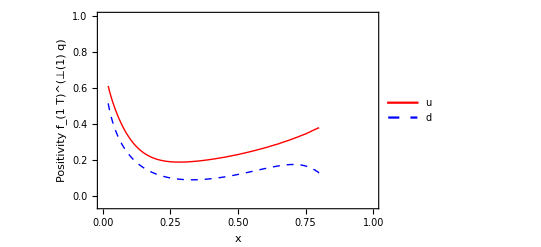

```mathematica
Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,1.}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity f_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.55}]]
```

```mathematica
Export["../tex/figs/sivers_proton_positivity.pdf",%,Background->None]
```

../tex/figs/sivers_proton_positivity.pdf

### Positivity Boer Mulders

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 MA^2))^1 h1Lperpa[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[h1LperpFirstMomenta^2/(4 ktah1La π),Re[ktah1La]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 MA^2))^1 h1perpa[kt^2])^2 ⅆphiⅆkt
```

((h_a^(FIRST perp))^2)/(4 k_aTBOERMULDERS^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 MA^2))^1 (f1a[kt^2])^2 ⅆphiⅆkt
```

f_a^2/(16 MA^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 MA^2))^1 (g1a[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g1a^2/(16 MA^2 π),Re[avktag1]>0]

```mathematica
Positivityu[x_,Q2_] := ((f1u[x,Q2])/(4 Mproton √π)-√((g1u[x,Q2])^2/(16 Mproton^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avkBM  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mproton √π)+√((g1u[x,Q2])^2/(16 Mproton^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avkBM  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mproton √π)-√((g1d[x,Q2])^2/(16 Mproton^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avkBM  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mproton √π)+√((g1d[x,Q2])^2/(16 Mproton^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avkBM  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))
```

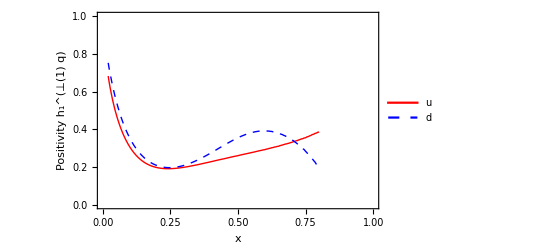

```mathematica
Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,1.}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity h_1^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.55}]]
```

```mathematica
Export["../tex/figs/boermulders_proton_positivity.pdf",%,Background->None]
```

../tex/figs/boermulders_proton_positivity.pdf

## Positivity pion functions

### Positivity Boer Mulders π^-(ubar,d)

```mathematica
PositivityubarPion[x_,Q2_] := (Sqrt[(piminusubar[x,Q2])^2]/(4 Mpion √π)-√((BoerMuldersPionFirstMoment[x,Q2])^2/(4 avkBM  π)))/(Sqrt[(piminusubar[x,Q2])^2]/(4 Mpion √π)+√((BoerMuldersPionFirstMoment[x,Q2])^2/(4 avkBM  π)))
```

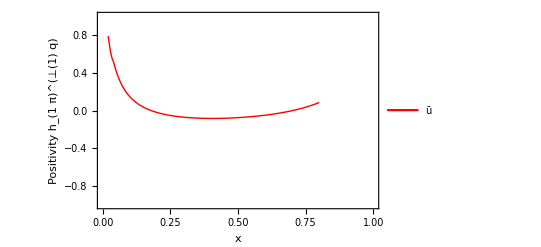

```mathematica
Plot[{PositivityubarPion[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-1.,1.}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity h_(1  π)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"ū"},{0.1,0.85}]]
```

```mathematica
Export["../tex/figs/boermulders_pion_positivity.pdf",%,Background->None]
```

../tex/figs/boermulders_pion_positivity.pdf

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function F_UU^1

## F_UU^1 analytical result:

```mathematica
Print["Eq(91)  C[f1 f1]"]
weightUU[kt_,qT_,phi_] := 1;
qTweightUU[kt_] := 1;
```

Eq(91)  C[f1 f1]

```mathematica
Print["Eq(91)  C[f1 f1]"]
ConvolutionTMD[weightUU,f1a,f1b]
```

Eq(91)  C[f1 f1]

(ⅇ^(-q_T^2/(k_aTA^2+k_bTA^2)) f_a f_b)/((k_aTA^2+k_bTA^2) π)

```mathematica
Print["Eq(4.1)  ∫ⅆ^2q_T C[f1a f1b]"]
qTConvolutionTMD[qTweightUU,weightUU,f1a,f1b]
```

Eq(4.1)  ∫ⅆ^2q_T C[f1a f1b]

f_a f_b

## F_UU^1 RHIC numerics A=proton, B=proton:

```mathematica
avpa = 0.25;
avpb = 0.25;
avqT= avpa+avpb;


FUU1[xa_,xb_,Q2_,qT_] := ((4.0/9.0)f1u[xa,Q2] f1ubar[xb,Q2] +(1.0/9.0)f1d[xa,Q2] f1dbar[xb,Q2]+(1.0/9.0)f1s[xa,Q2] f1sbar[xb,Q2]  + (4.0/9.0)f1ubar[xa,Q2] f1ubar[xb,Q2]+(1.0/9.0)f1dbar[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1sbar[xa,Q2]f1s[xb,Q2])Exp[(-qT^2/avqT)]/(π avqT) 

FUU1Integrated[xa_,xb_,Q2_] := ((4.0/9.0)f1u[xa,Q2] f1ubar[xb,Q2] +(1.0/9.0)f1d[xa,Q2] f1dbar[xb,Q2]+(1.0/9.0)f1s[xa,Q2] f1sbar[xb,Q2]  + (4.0/9.0)f1ubar[xa,Q2] f1ubar[xb,Q2]+(1.0/9.0)f1dbar[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1sbar[xa,Q2]f1s[xb,Q2])
```

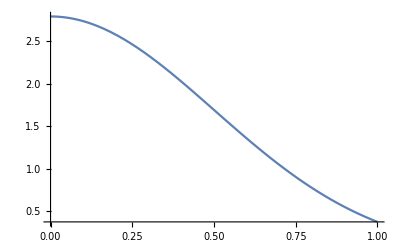

```mathematica
Plot[FUU1[0.1,0.1,1,qT],{qT,0,1}]
```

## F_UU^1 COMPASS numerics A=pion-, B=proton:

```mathematica
avpa = 0.25; (*assumption width pion == width proton!!*)
avpb = 0.25;
avqT= avpa+avpb;


FUU1pion[xa_,xb_,Q2_,qT_] := ((4.0/9.0)piminusu[xa,Q2] f1ubar[xb,Q2] +(1.0/9.0)piminusd[xa,Q2] f1dbar[xb,Q2]+(1.0/9.0)piminuss[xa,Q2] f1sbar[xb,Q2]  + (4.0/9.0)piminusubar[xa,Q2] f1ubar[xb,Q2]+(1.0/9.0)piminusdbar[xa,Q2] f1d[xb,Q2] +(1.0/9.0)piminussbar[xa,Q2]f1s[xb,Q2])Exp[(-qT^2/avqT)]/(π avqT) 

FUU1pionIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)piminusu[xa,Q2] f1ubar[xb,Q2] +(1.0/9.0)piminusd[xa,Q2] f1dbar[xb,Q2]+(1.0/9.0)piminuss[xa,Q2] f1sbar[xb,Q2]  + (4.0/9.0)piminusubar[xa,Q2] f1ubar[xb,Q2]+(1.0/9.0)piminusdbar[xa,Q2] f1d[xb,Q2] +(1.0/9.0)piminussbar[xa,Q2]f1s[xb,Q2])
```

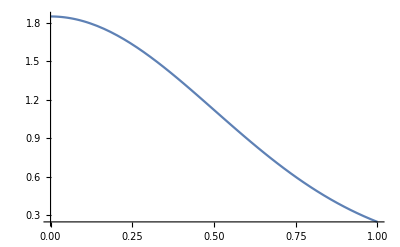

```mathematica
Plot[FUU1pion[0.1,0.1,1,qT],{qT,0,1}]
```

Phenomenology of leading twist single spin asymmetry A_UT^1 Sivers COMPASS

## A_UT^1 analytical result:

```mathematica
Print["Eq(98)  C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ]"  ]
weightUT1[kt_,qT_,phi_] := (qT-kt Cos[phi])/MB;
qTweightUT1[kt_] := 1;
```

Eq(98)  C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ]

```mathematica
Print["Eq(99)  F_UT^(TraditionalForm`1)= C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ] ="  ]
ConvolutionTMD[weightUT1,f1a,f1Tperpb]
```

Eq(99)  F_UT^(TraditionalForm`1)= C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ] =

(2 ⅇ^(-q_T^2/(k_aTA^2+k_bTSIVERS^2)) f_a f_Tb^(FIRST perp) MB q_T)/((k_aTA^2+k_bTSIVERS^2)^2 π)

```mathematica
Print["Eq(99)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ] ="  ]
qTConvolutionTMD[qTweightUT1,weightUT1,f1a,f1Tperpb]
```

Eq(99)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T C[ (h̄)/M_b  f_(1  a) OverBar[f_(1  T b)^⊥] ] =

(f_a f_Tb^(FIRST perp) MB √π)/(√(k_aTA^2+k_bTSIVERS^2))

## A_UT^1 COMPASS parametrization for A=pion - (ubar,d), B=proton:

```mathematica
Mb = Mpion; (*pion*)

avUT1:= avks+avk;

gUT1[qT_] := (2 Mb qT)/(π avUT1^2) Exp[(-qT^2/avUT1)]
aUT1 := (Mb √π)/(√avUT1)  

FUT1pion[xa_,xb_,Q2_,qT_] := ((4.0/9.0)piminusubar[xa,Q2]f1TperpuFirstMoment[xb,Q2]  +

(4.0/9.0)piminusu[xa,Q2]f1TperpubarFirstMoment[xb,Q2]  +(1.0/9.0)piminusdbar[xa,Q2]f1TperpdFirstMoment[xb,Q2]  +

(1.0/9.0)piminusd[xa,Q2]f1TperpdbarFirstMoment[xb,Q2]  +(1.0/9.0)piminussbar[xa,Q2]f1TperpsFirstMoment[xb,Q2]  +

(1.0/9.0)piminuss[xa,Q2]f1TperpsbarFirstMoment[xa,Q2]) gUT1[qT]


FUT1Integratedpion[xa_,xb_,Q2_] := ((4.0/9.0)piminusubar[xa,Q2]f1TperpuFirstMoment[xb,Q2]  +

(4.0/9.0)piminusu[xa,Q2]f1TperpubarFirstMoment[xb,Q2]  +(1.0/9.0)piminusdbar[xa,Q2]f1TperpdFirstMoment[xb,Q2]  +

(1.0/9.0)piminusd[xa,Q2]f1TperpdbarFirstMoment[xb,Q2]  +(1.0/9.0)piminussbar[xa,Q2]f1TperpsFirstMoment[xb,Q2]  +

(1.0/9.0)piminuss[xa,Q2]f1TperpsbarFirstMoment[xa,Q2]) aUT1
```

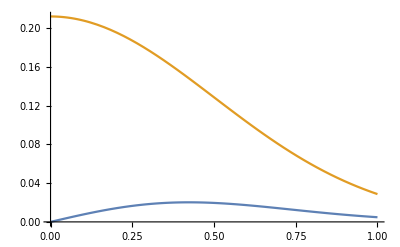

```mathematica
Plot[{FUT1pion[0.1,0.3,1,PT],FUU1pion[0.1,0.3,1,PT]},{PT,0,1}]
```

## A_TU^1 COMPASS numerics for A=pion - (ubar,d), B=proton:

```mathematica
AUT1pion[xa_,xb_,Q2_,qT_] := FUT1pion[xa,xb, Q2,qT]/FUU1pion[xa,xb, Q2,qT];

AUT1pionIntegrated[xa_,xb_,Q2_] := FUT1Integratedpion[xa,xb, Q2]/FUU1pionIntegrated[xa,xb, Q2];
```

### Plot of xa = xpion dependence

```mathematica
AUT1pionIntegrated[x_] :=AUT1pionIntegrated[x,0.16,25];
```

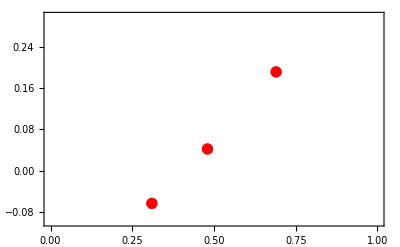

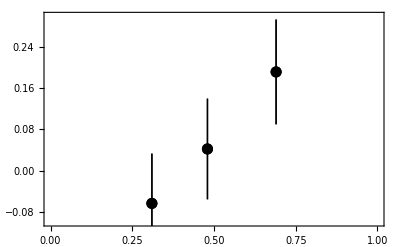

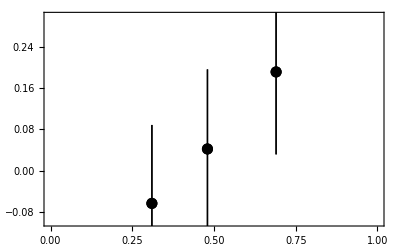

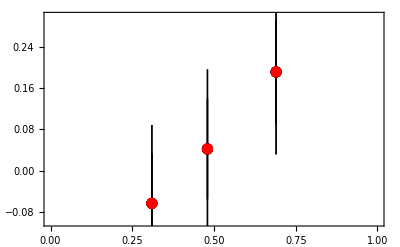

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

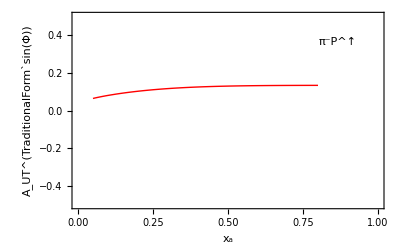

```mathematica
AUT1sinphiplot = Plot[AUT1pionIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

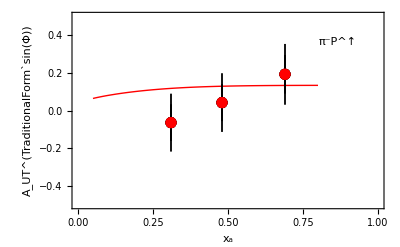

```mathematica
Show[AUT1sinphiplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsinphi_xpi.pdf",%,Background->None]
```

../tex/figs/AUTsinphi_xpi.pdf

### Plot of xb = xN dependence

```mathematica
AUT1pionIntegrated[x_] :=AUT1pionIntegrated[0.47,x,25];
```

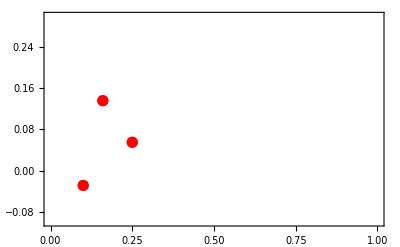

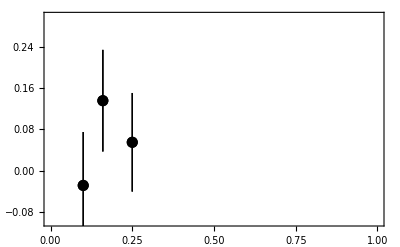

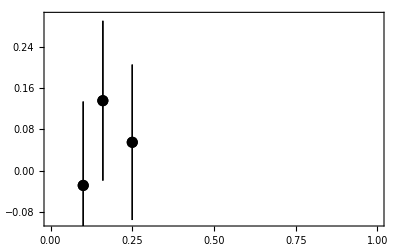

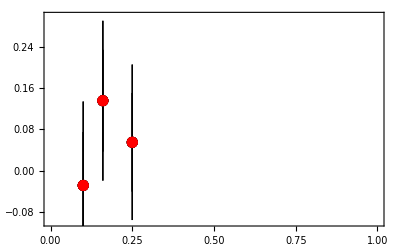

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

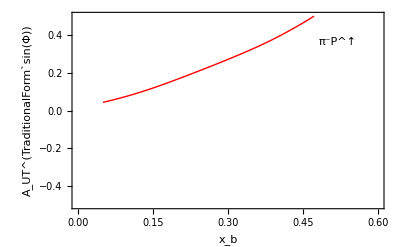

```mathematica
AUT1sinphiplot = Plot[AUT1pionIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.6},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_b","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

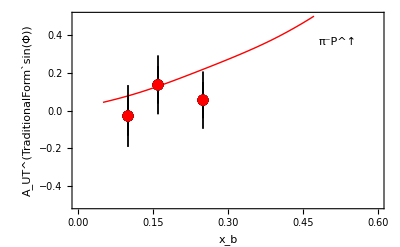

```mathematica
Show[AUT1sinphiplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsinphi_xN.pdf",%,Background->None]
```

../tex/figs/AUTsinphi_xN.pdf

### Plot of qT dependence

```mathematica
AUT1pion[qT_] :=AUT1pion[0.5,0.17,25,qT];
```

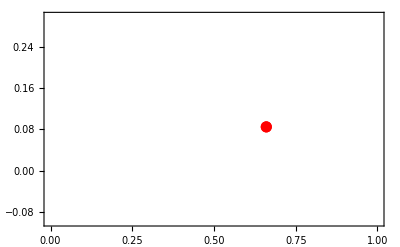

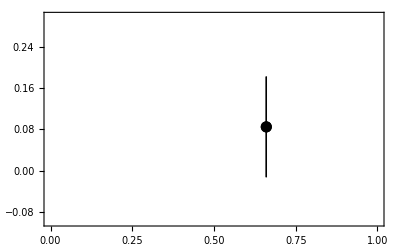

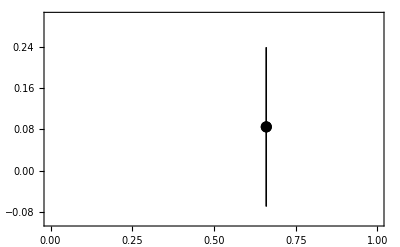

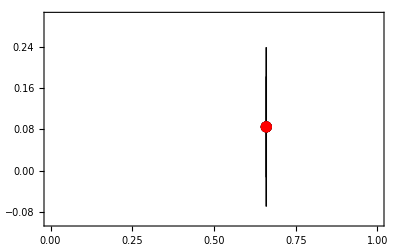

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

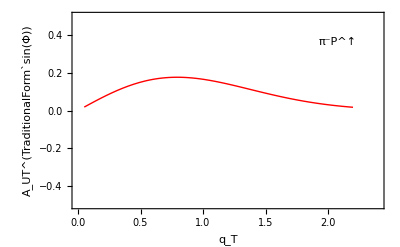

```mathematica
AUT1sinphiplot = Plot[AUT1pion[x],{x,0.05,2.2},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2.4},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

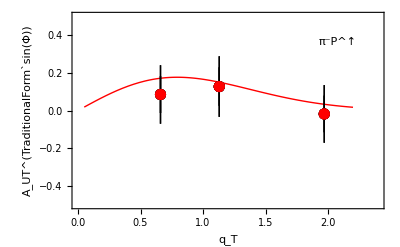

```mathematica
Show[AUT1sinphiplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsinphi_qT.pdf",%,Background->None]
```

../tex/figs/AUTsinphi_qT.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[2Φ-Φ_b]COMPASS

## A_UT^sin[2Φ-Φ_b] analytical result:

```mathematica
Print["Eq(99)  -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ]"  ]
weightUTsin2phi[kt_,PhT_,phi_] := -(kt Cos[phi])/MA;
qTweightUTsin2phi[kt_] := 1;
```

Eq(99)  -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ]

```mathematica
Print["Eq(99)  F_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] ="  ]
ConvolutionTMD[weightUTsin2phi,h1perpa,h1b]
```

Eq(99)  F_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] =

-(2 ⅇ^(-q_T^2/(k_aTBOERMULDERS^2+k_bTh1^2)) h_a^(FIRST perp) h_b MA q_T)/((k_aTBOERMULDERS^2+k_bTh1^2)^2 π)

```mathematica
Print["Eq(99)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] ="  ]
qTConvolutionTMD[qTweightUTsin2phi,weightUTsin2phi,h1perpa,h1b]
```

Eq(99)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] =

-(h_a^(FIRST perp) h_b MA √π)/(√(k_aTBOERMULDERS^2+k_bTh1^2))

## A_UT^sin[2Φ-Φ_a] parametrization for A=pion - (ubar,d), B=proton:

```mathematica
Ma = Mpion; (*pion*)

avUTsin2phiPT:= avkBM+avk;

gUTsin2phi[qT_] := -(2 Ma qT)/(π avUTsin2phiPT^2) Exp[(-qT^2/avUTsin2phiPT)]
aUTsin2phi := -(Ma √π)/(√avUTsin2phiPT)  

FUTpionsin2phi[xa_,xb_,Q2_,qT_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xa,Q2] h1u[xb,Q2] ) gUTsin2phi[qT]


FUTpionsin2phiIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xa,Q2] h1u[xb,Q2] ) aUTsin2phi
```

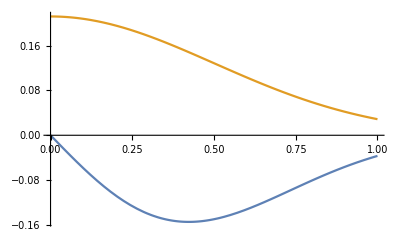

```mathematica
Plot[{FUTpionsin2phi[0.1,0.3,1,PT],FUU1pion[0.1,0.3,1,PT]},{PT,0,1}]
```

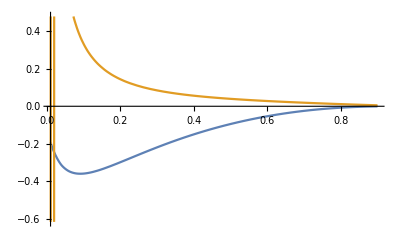

```mathematica
Plot[{FUTpionsin2phiIntegrated[xa,0.3,1],FUU1pionIntegrated[xa,0.3,1]},{xa,0.01,0.9}]
```

## A_UT^sin[2Φ-Φ_a]COMPASS numerics for A=pion - (ubar,d), B=proton:

```mathematica
AUTpionsin2phi[xa_,xb_,Q2_,qT_] := FUTpionsin2phi[xa,xb, Q2,qT]/FUU1pion[xa,xb, Q2,qT];

AUTpionsin2phiIntegrated[xa_,xb_,Q2_] := FUTpionsin2phiIntegrated[xa,xb, Q2]/FUU1pionIntegrated[xa,xb, Q2];
```

### Plot of xa = xpion dependence

```mathematica
AUTpionsin2phiIntegrated[x_] :=AUTpionsin2phiIntegrated[x,0.17,25];
```

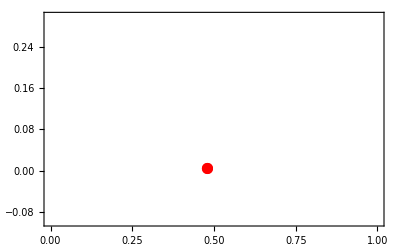

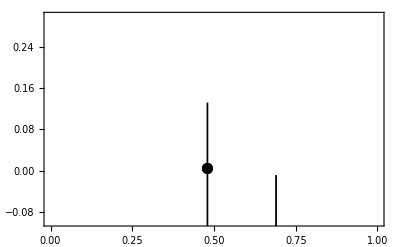

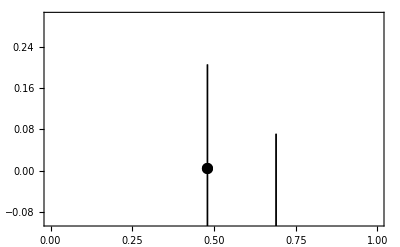

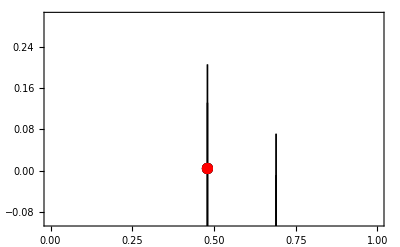

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

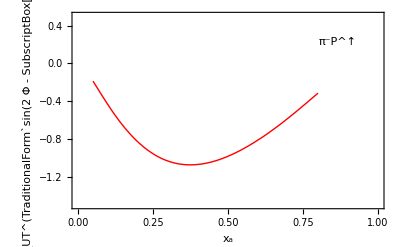

```mathematica
AUT1sinphiplot = Plot[AUTpionsin2phiIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-1.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

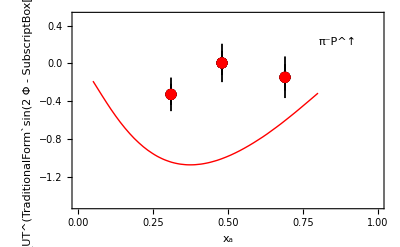

```mathematica
Show[AUT1sinphiplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_m_phiS_xpi.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_m_phiS_xpi.pdf

### Plot of xb = xN dependence

```mathematica
AUTpionsin2phiIntegrated[x_] :=AUTpionsin2phiIntegrated[0.47,x,25];
```

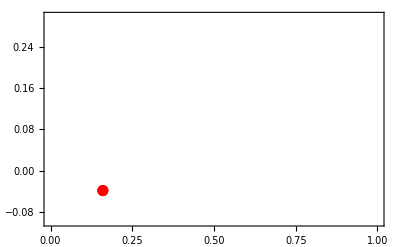

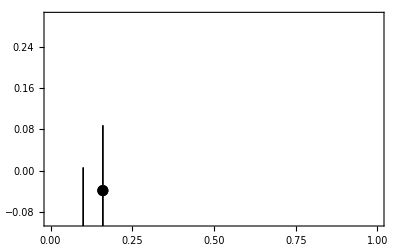

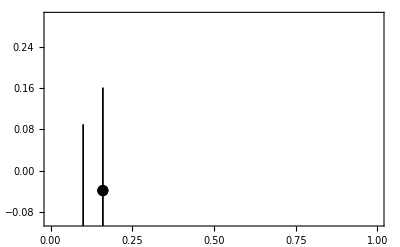

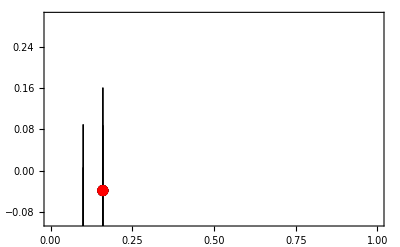

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

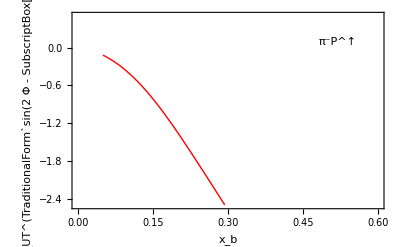

```mathematica
AUTpionsin2phiplot = Plot[AUTpionsin2phiIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.6},{-2.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_b","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

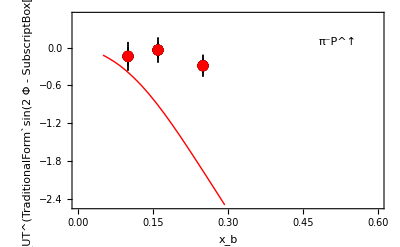

```mathematica
Show[AUTpionsin2phiplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_m_phiS_xN.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_m_phiS_xN.pdf

### Plot of qT dependence

```mathematica
AUTpionsin2phi[qT_] :=AUTpionsin2phi[0.5,0.17,25,qT];
```

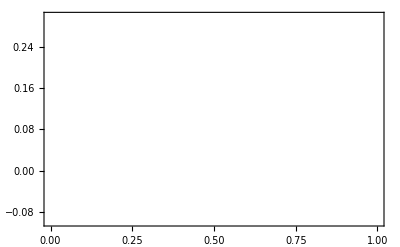

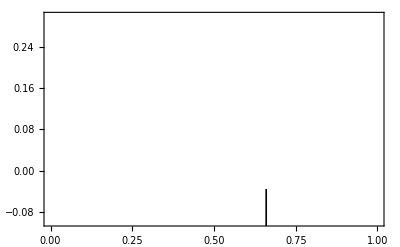

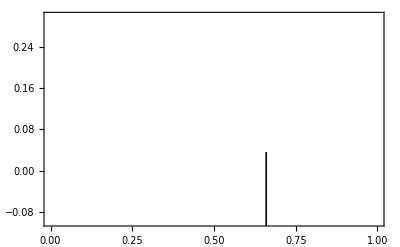

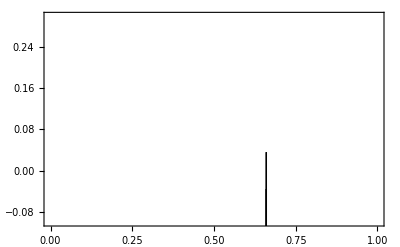

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

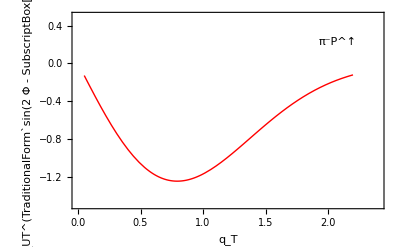

```mathematica
AUTpionsin2phiplot = Plot[AUTpionsin2phi[x],{x,0.05,2.2},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2.4},{-1.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

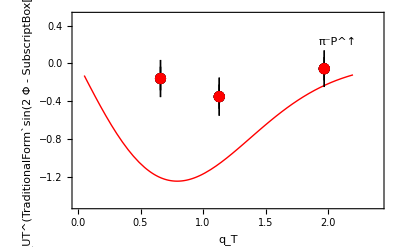

```mathematica
Show[AUTpionsin2phiplot , plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_m_phiS_qT.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_m_phiS_qT.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[2Φ+Φ_b]COMPASS

## A_UT^sin[2Φ+Φ_b] analytical result:

```mathematica
Print["Eq(100)  -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ]"  ]
weightUTsin2phiplusphib[kt_,qT_,phi_] := 1/(2 MB^2 MA)(2(qT-kt Cos[phi])(2kt Cos[phi](qT-kt Cos[phi])-(kt qT Cos[phi]-kt^2))-kt Cos[phi](qT-kt Cos[phi])^2);
qTweightUTsin2phiplusphib[kt_] := 1;
```

Eq(100)  -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ]

```mathematica
Print["Eq(100)  F_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ]"  ]
ConvolutionTMD[weightUTsin2phiplusphib,h1perpa,h1Tperpb]
```

Eq(100)  F_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ]

(ⅇ^(-q_T^2/(k_aTBOERMULDERS^2+k_bTPRETZELOSITY^2)) h_a^(FIRST perp) h_Tb^(perp SECOND) MA MB^2 q_T (k_aTBOERMULDERS^2 (k_aTBOERMULDERS^2+k_bTPRETZELOSITY^2)+2 k_bTPRETZELOSITY^2 q_T^2))/(k_bTPRETZELOSITY^2 (k_aTBOERMULDERS^2+k_bTPRETZELOSITY^2)^4 π)

```mathematica
Print["Eq(97)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ] ="  ]
qTConvolutionTMD[qTweightUTsin2phiplusphib,weightUTsin2phiplusphib,h1perpa,h1Tperpb]
```

Eq(97)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (2 OverscriptBox[h, _] . SubscriptBox[k, bT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, bT, 2] (OverscriptBox[h, _] . SubscriptBox[k, aT]))/(2 SubsuperscriptBox[M, b, 2] SubscriptBox[M, a])  h_(1  a)^⊥ OverBar[h_(1  T b)^⊥] ] =

(h_a^(FIRST perp) h_Tb^(perp SECOND) (k_aTBOERMULDERS^2+3 k_bTPRETZELOSITY^2) MA MB^2 √π)/(2 k_bTPRETZELOSITY^2 (k_aTBOERMULDERS^2+k_bTPRETZELOSITY^2)^(3/2))

## A_UT^sin[2Φ+Φ_a] parametrization for A=pion - (ubar,d), B=proton:

```mathematica
Ma = Mpion; (*pion*)
Mb = Mproton; (*proton*)
avkBMa = avkBM;
avkPb = avkTT;


avUTsin2phiplusphibPT:= avkBMa+avkPb;

gUTsin2phiplusphib[qT_] := (2 Ma Mb^2 qT(avkBMa avUTsin2phiplusphibPT^2 + 2 avkPb  qT^2))/(π avkPb avUTsin2phiplusphibPT^4) Exp[(-qT^2/avUTsin2phiplusphibPT)]
aUTsin2phiplusphib := Ma Mb^2  (3 avkPb+avkBMa)√π/( 2 avkPb √(avUTsin2phiplusphibPT^3))  

FUTsin2phiplusphib[xa_,xb_,Q2_,qT_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xa,Q2] h1TperpuSecondMoment[xb,Q2]) gUTsin2phiplusphib[qT]


FUTsin2phiplusphibIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xa,Q2] h1TperpuSecondMoment[xb,Q2]) aUTsin2phiplusphib
```

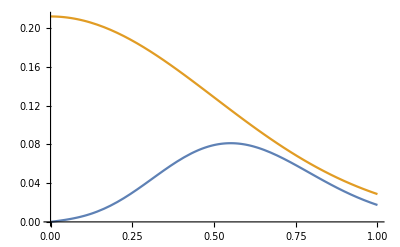

```mathematica
Plot[{FUTsin2phiplusphib[0.1,0.3,1,PT],FUU1pion[0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[2Φ+Φ_a]COMPASS numerics for A=pion - (ubar,d), B=proton:

```mathematica
AUTsin2phiplusphib[xa_,xb_,Q2_,qT_] := FUTsin2phiplusphib[xa,xb, Q2,qT]/FUU1pion[xa,xb, Q2,qT];

AUTsin2phiplusphibIntegrated[xa_,xb_,Q2_] := FUTsin2phiplusphibIntegrated[xa,xb, Q2]/FUU1pionIntegrated[xa,xb, Q2];
```

### Plot of xa = xpion dependence

```mathematica
AUTsin2phiplusphibIntegrated[x_] :=AUTsin2phiplusphibIntegrated[x,0.16,25];
```

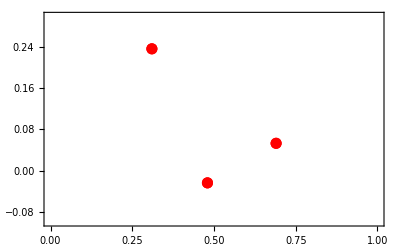

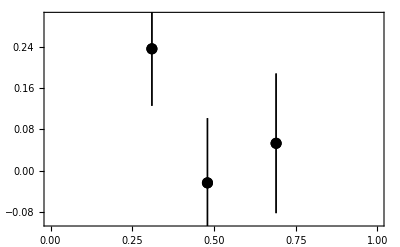

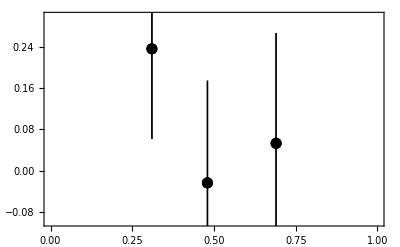

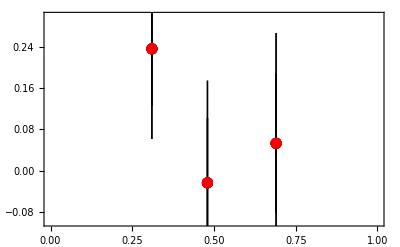

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_p_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

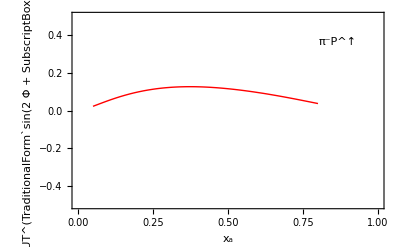

```mathematica
AUTsin2phiplusphibplot = Plot[AUTsin2phiplusphibIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

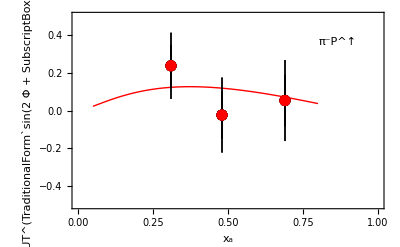

```mathematica
Show[AUTsin2phiplusphibplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_p_phiS_xpi.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_p_phiS_xpi.pdf

### Plot of xb = xN dependence

```mathematica
AUTsin2phiplusphibIntegrated[x_] :=AUTsin2phiplusphibIntegrated[0.47,x,25];
```

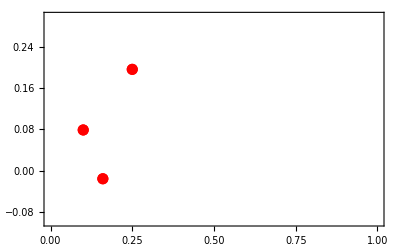

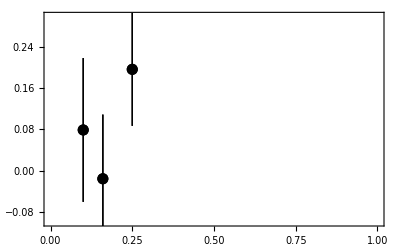

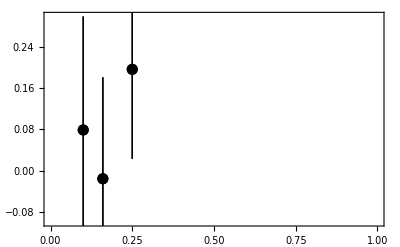

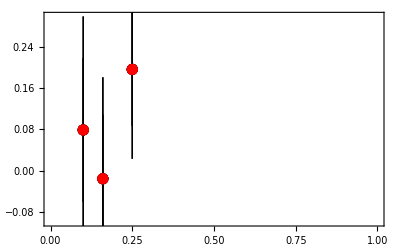

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_p_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

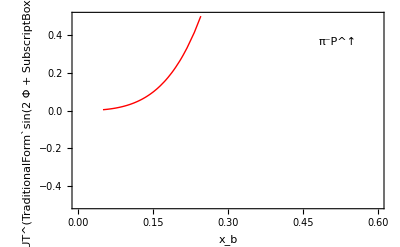

```mathematica
AUTsin2phiplusphibplot = Plot[AUTsin2phiplusphibIntegrated[x],{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.6},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_b","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

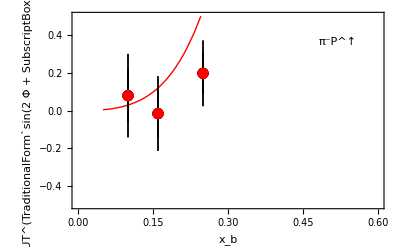

```mathematica
Show[AUTsin2phiplusphibplot, plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_p_phiS_xN.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_p_phiS_xN.pdf

### Plot of qT dependence

```mathematica
AUTsin2phiplusphib[qT_] :=AUTsin2phiplusphib[0.5,0.17,25,qT];
```

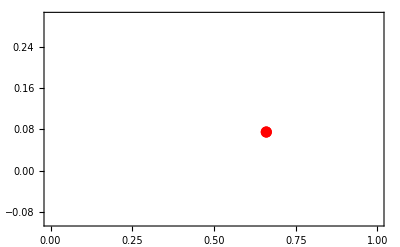

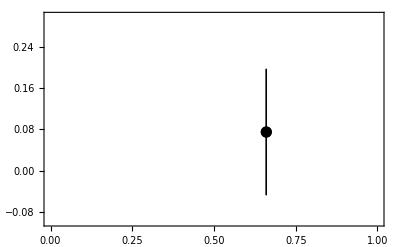

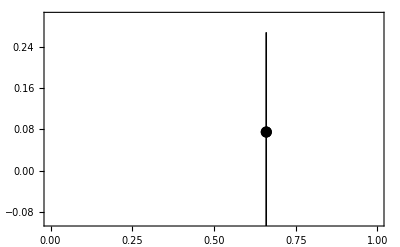

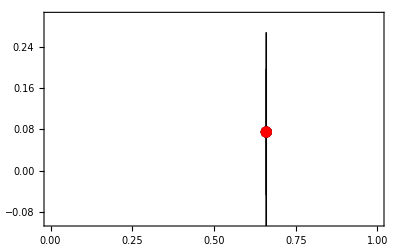

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_p_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

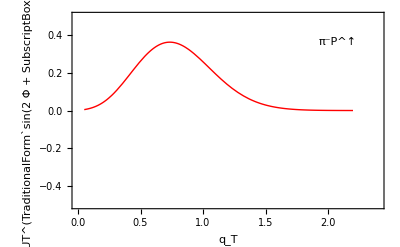

```mathematica
AUTsin2phiplusphibplot = Plot[AUTsin2phiplusphib[x],{x,0.05,2.2},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2.4},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, a]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["π^-P^↑",{0.85,0.85}]]
```

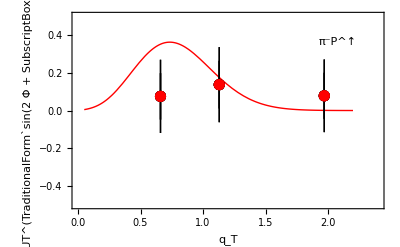

```mathematica
Show[AUTsin2phiplusphibplot , plotdata]
```

```mathematica
Export["../tex/figs/AUTsin2phi_p_phiS_qT.pdf",%,Background->None]
```

../tex/figs/AUTsin2phi_p_phiS_qT.pdf

Phenomenology of leading twist single spin asymmetry A_TU^1 Sivers RHIC

## A_TU^1 RHIC analytical result:

```mathematica
Print["Eq(95)  -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ]"  ]
weightUT1[kt_,PhT_,phi_] := -(kt Cos[phi])/MA;
qTweightUT1[kt_] := 1;
```

Eq(95)  -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ]

```mathematica
Print["Eq(99)  F_TU^(TraditionalForm`1)= -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] ="  ]
ConvolutionTMD[weightUT1,f1Tperpa,f1b]
```

Eq(99)  F_TU^(TraditionalForm`1)= -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] =

-(2 ⅇ^(-q_T^2/(k_bTA^2+k_aTSIVERS^2)) f_b f_Ta^(FIRST perp) MA q_T)/((k_bTA^2+k_aTSIVERS^2)^2 π)

```mathematica
Print["Eq(95)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] ="  ]
qTConvolutionTMD[qTweightUT1,weightUT1,f1Tperpa,f1b]
```

Eq(95)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] =

-(f_b f_Ta^(FIRST perp) MA √π)/(√(k_bTA^2+k_aTSIVERS^2))

## A_TU^1 RHIC numerics for A=polarized proton, B=proton:

```mathematica
Ma = Mproton; (*proton*)

avTU1:= avks+avk;

gTU1[qT_] := -(2 Ma qT)/(π avTU1^2) Exp[(-qT^2/avTU1)]
aTU1 := -(Ma √π)/(√avTU1)  

FTU1[xa_,xb_,Q2_,qT_] := ((4.0/9.0)f1TperpuFirstMoment[xa,Q2] f1ubar[xb,Q2] +

(4.0/9.0)f1TperpubarFirstMoment[xa,Q2] f1u[xb,Q2] +(1.0/9.0)f1TperpdFirstMoment[xa,Q2] f1dbar[xb,Q2] +

(1.0/9.0)f1TperpdbarFirstMoment[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1TperpsFirstMoment[xa,Q2] f1sbar[xb,Q2] +

(1.0/9.0)f1TperpsbarFirstMoment[xa,Q2] f1s[xb,Q2]) gTU1[qT]


FTU1Integrated[xa_,xb_,Q2_] := ((4.0/9.0)f1TperpuFirstMoment[xa,Q2] f1ubar[xb,Q2] +

(4.0/9.0)f1TperpubarFirstMoment[xa,Q2] f1u[xb,Q2] +(1.0/9.0)f1TperpdFirstMoment[xa,Q2] f1dbar[xb,Q2] +

(1.0/9.0)f1TperpdbarFirstMoment[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1TperpsFirstMoment[xa,Q2] f1sbar[xb,Q2] +

(1.0/9.0)f1TperpsbarFirstMoment[xa,Q2] f1s[xb,Q2]) aTU1
```

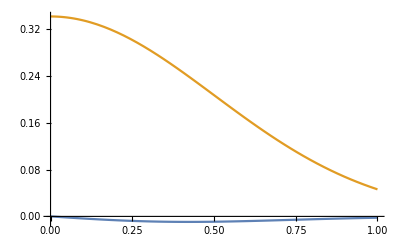

```mathematica
Plot[{FTU1[0.1,0.3,1,PT],FUU1[0.1,0.3,1,PT]},{PT,0,1}]
```

Phenomenology of leading twist single spin asymmetry A_TU^sin[2Φ-Φ_b]RHIC

## A_TU^sin[2Φ-Φ_b] analytical result:

```mathematica
Print["Eq(99)  -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ]"  ]
weightUTsin2phi[kt_,PhT_,phi_] := -(kt Cos[phi])/MA;
qTweightUTsin2phi[kt_] := 1;
```

Eq(99)  -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ]

```mathematica
Print["Eq(99)  F_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] ="  ]
ConvolutionTMD[weightUTsin2phi,h1perpa,h1b]
```

Eq(99)  F_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] =

-(2 ⅇ^(-q_T^2/(k_aTBOERMULDERS^2+k_bTh1^2)) h_a^(FIRST perp) h_b MA q_T)/((k_aTBOERMULDERS^2+k_bTh1^2)^2 π)

```mathematica
Print["Eq(99)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] ="  ]
qTConvolutionTMD[qTweightUTsin2phi,weightUTsin2phi,h1perpa,h1b]
```

Eq(99)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ - SubscriptBox[Φ, b]])= ∫ⅆ^2q_T -C[ (h̄)/M_a  h_(1  a)^⊥ (h̄)_(1  b) ] =

-(h_a^(FIRST perp) h_b MA √π)/(√(k_aTBOERMULDERS^2+k_bTh1^2))

## A_TU^sin[2Φ-Φ_a] numerics for A=proton, B=proton:

```mathematica
Ma = Mproton; (*proton*)

avTUsin2phiPT:= avkBM+avk;

gTUsin2phi[qT_] := -(2 Mp^2 qT)/(π Ma avTUsin2phiPT^2) Exp[(-qT^2/avTUsin2phiPT)]
aTUsin2phi := -(Mp^2 √π)/(Ma √avTUsin2phiPT)  

FTUsin2phi[xa_,xb_,Q2_,qT_] := ((4.0/9.0)h1perpubarFirstMoment[xa,Q2] h1u[xb,Q2] +(1.0/9.0)h1perpdbarFirstMoment[xa,Q2] h1d[xb,Q2]) gTUsin2phi[qT]


FTUsin2phiIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)h1perpubarFirstMoment[xa,Q2] h1u[xb,Q2] +(1.0/9.0)h1perpdbarFirstMoment[xa,Q2] h1d[xb,Q2]) aTUsin2phi
```

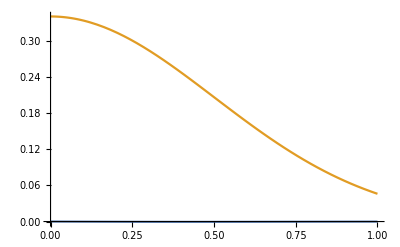

```mathematica
Plot[{FTUsin2phi[0.1,0.3,1,PT],FUU1[0.1,0.3,1,PT]},{PT,0,1}]
```

## A_TU^sin[2Φ-Φ_a]numerics:

```mathematica
ATUsin2phi[xa_,xb_,Q2_,qT_] := FTUsin2phi[xa,xb, Q2,qT]/FUU1[xa,xb, Q2,qT];

ATUsin2phiIntegrated[xa_,xb_,Q2_] := FTUsin2phiIntegrated[xa,xb, Q2]/FUU1Integrated[xa,xb, Q2];
```

### Plot of qT dependence

```mathematica
ATUsin2phifuncqT[qT_] :=ATUsin2phi[0.25,0.54,12.4, qT];
```

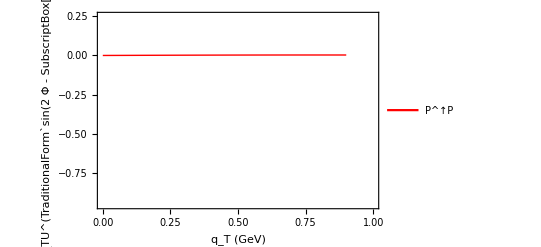

```mathematica
ATUsin2phiplotqT = Plot[{ATUsin2phifuncqT[qT]},{qT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.95,0.25}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T (GeV)","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P^↑P"},{0.7,0.15}]]
```

```mathematica
Show[ATUsin2phiplotqT]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phi_qT.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_qT.pdf

### Plot of x dependence

```mathematica
ATUsin2phifuncIntegrated[x_] :=ATUsin2phiIntegrated[x,0.54,12.4];
```

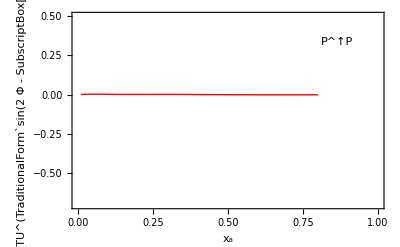

```mathematica
ATUsin2phiplot = Plot[{ATUsin2phiIntegrated[x,0.54,12.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.7,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑P",{0.85,0.85}]]
```

```mathematica
Show[ATUsin2phiplot]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phi_x.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_x.pdf

## A_TU^sin[2Φ-Φ_a] numerics for A= proton, B=pion-(ubar,d):

```mathematica
Ma = Mproton; (*proton*)

avTUsin2phiPT:= avkBM+avk;

gTUsin2phi[qT_] := -(2 Mp^2 qT)/(π Ma avTUsin2phiPT^2) Exp[(-qT^2/avTUsin2phiPT)]
aTUsin2phi := -(Mp^2 √π)/(Ma √avTUsin2phiPT)  

FTUpionsin2phi[xa_,xb_,Q2_,qT_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xb,Q2] h1u[xa,Q2] ) gTUsin2phi[qT]


FTUpionsin2phiIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)BoerMuldersPionFirstMoment[xb,Q2] h1u[xa,Q2] ) aTUsin2phi
```

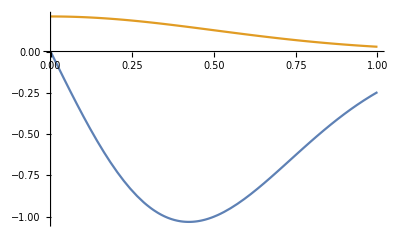

```mathematica
Plot[{FTUpionsin2phi[0.1,0.3,1,PT],FUU1pion[0.1,0.3,1,PT]},{PT,0,1}]
```

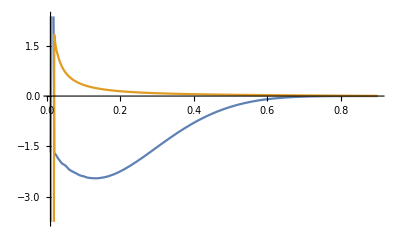

```mathematica
Plot[{FTUpionsin2phiIntegrated[xa,0.3,1],FUU1pionIntegrated[xa,0.3,1]},{xa,0.01,0.9}]
```

## A_TU^sin[2Φ-Φ_a]numerics for A= proton, B=pion-(ubar,d):

```mathematica
ATUpionsin2phi[xa_,xb_,Q2_,qT_] := FTUpionsin2phi[xa,xb, Q2,qT]/FUU1pion[xa,xb, Q2,qT];

ATUpionsin2phiIntegrated[xa_,xb_,Q2_] := FTUpionsin2phiIntegrated[xa,xb, Q2]/FUU1pionIntegrated[xa,xb, Q2];
```

### Plot of qT dependence

```mathematica
ATUpionsin2phifuncqT[qT_] :=ATUpionsin2phi[0.17,0.5,25., qT];
```

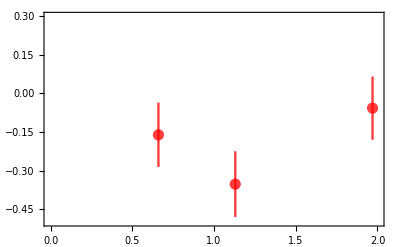

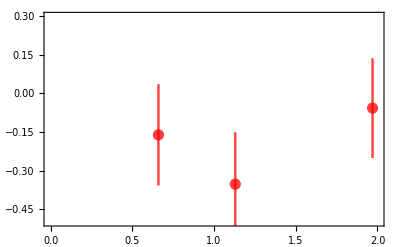

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,2.},{-0.5,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,2.},{-0.5,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

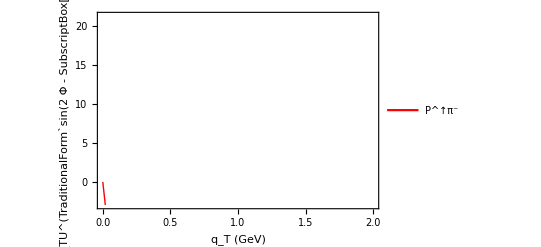

```mathematica
ATUpionsin2phiplotqT = Plot[{ATUpionsin2phifuncqT[qT]},{qT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2},{-2.95,21.25}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T (GeV)","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P^↑π^-"},{0.7,0.15}]]
```

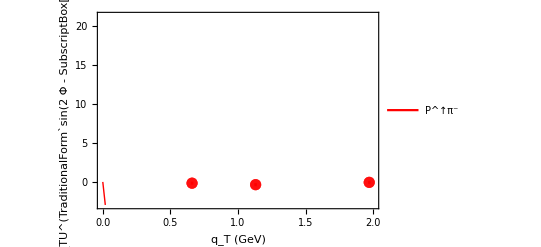

```mathematica
Show[ATUpionsin2phiplotqT, plotdataCOMPASSpim, plotdataCOMPASSpimsys]
```

```mathematica
Export["../tex/figs/ATUsin2phi_qT.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_qT.pdf

### Plot of xb = xpion dependence

```mathematica
ATUsin2phifuncIntegrated[x_] :=ATUpionsin2phiIntegrated[0.2,x,25];
```

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

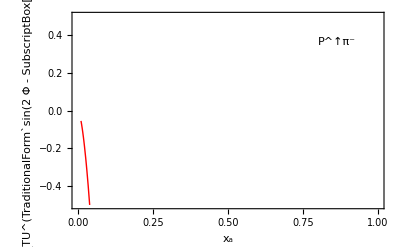

```mathematica
ATUsin2phiplot = Plot[ATUsin2phifuncIntegrated[x],{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.5,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑π^-",{0.85,0.85}]]
```

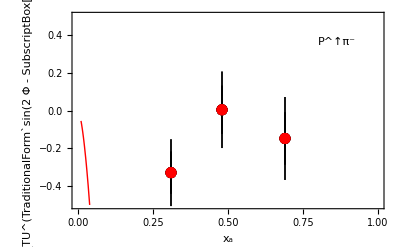

```mathematica
Show[ATUsin2phiplot, plotdata]
```

```mathematica
Export["../tex/figs/ATUsin2phi_xpi.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_xpi.pdf

### Plot of xa = xN dependence

```mathematica
ATUsin2phifuncIntegrated[x_] :=ATUpionsin2phiIntegrated[x,0.5,25];
```

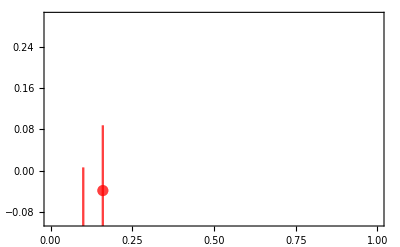

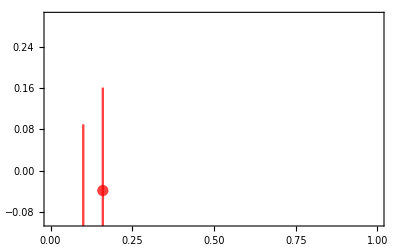

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

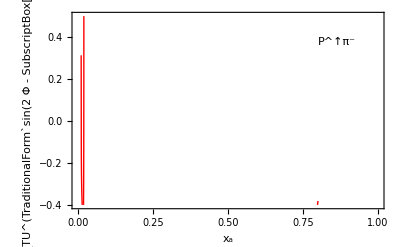

```mathematica
ATUsin2phiplot = Plot[ATUsin2phifuncIntegrated[x],{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.4,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑π^-",{0.85,0.85}]]
```

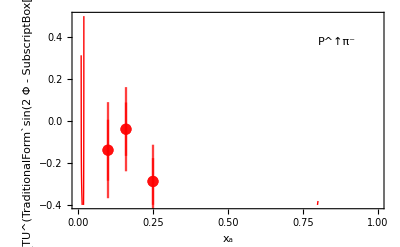

```mathematica
Show[ATUsin2phiplot, plotdataCOMPASSpim, plotdataCOMPASSpimsys]
```

```mathematica
Export["../tex/figs/ATUsin2phi_xN.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_xN.pdf

Phenomenology of leading twist single spin asymmetry A_TU^1 Sivers RHIC

## A_TU^1 RHIC analytical result:

```mathematica
Print["Eq(98)  -C[ (h̄)/M_a  f_(1  a)^⊥ (D̄)_(1  b) ]"  ]
weightUT1[kt_,PhT_,phi_] := -(kt Cos[phi])/MA;
qTweightUT1[kt_] := 1;
```

Eq(98)  -C[ (h̄)/M_a  f_(1  a)^⊥ (D̄)_(1  b) ]

```mathematica
Print["Eq(99)  F_TU^(TraditionalForm`1)= -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] ="  ]
ConvolutionTMD[weightUT1,f1Tperpa,f1b]
```

Eq(99)  F_TU^(TraditionalForm`1)= -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] =

-(2 ⅇ^(-q_T^2/(k_bTA^2+k_aTSIVERS^2)) f_b f_Ta^(FIRST perp) MA q_T)/((k_bTA^2+k_aTSIVERS^2)^2 π)

```mathematica
Print["Eq(99)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] ="  ]
qTConvolutionTMD[qTweightUT1,weightUT1,f1Tperpa,f1b]
```

Eq(99)  ∫ⅆ^2q_TF_TU^(TraditionalForm`1)= ∫ⅆ^2q_T -C[ (h̄)/M_a  f_(1  a)^⊥ (f̄)_(1  b) ] =

-(f_b f_Ta^(FIRST perp) MA √π)/(√(k_bTA^2+k_aTSIVERS^2))

## A_TU^1 RHIC numerics for A=proton, B=proton:

```mathematica
Ma = Mp; (*proton*)

avTU1:= avks+avk;

gTU1[qT_] := -(2 Mp^2 qT)/(π Ma avTU1^2) Exp[(-qT^2/avTU1)]
aTU1 := -(Mp^2 √π)/(Ma √avTU1)  

FTU1[xa_,xb_,Q2_,qT_] := ((4.0/9.0)f1TperpuFirstMoment[xa,Q2] f1ubar[xb,Q2] +

(4.0/9.0)f1TperpubarFirstMoment[xa,Q2] f1u[xb,Q2] +(1.0/9.0)f1TperpdFirstMoment[xa,Q2] f1dbar[xb,Q2] +

(1.0/9.0)f1TperpdbarFirstMoment[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1TperpsFirstMoment[xa,Q2] f1sbar[xb,Q2] +

(1.0/9.0)f1TperpsbarFirstMoment[xa,Q2] f1s[xb,Q2]) gTU1[qT]


FTU1Integrated[xa_,xb_,Q2_] := ((4.0/9.0)f1TperpuFirstMoment[xa,Q2] f1ubar[xb,Q2] +

(4.0/9.0)f1TperpubarFirstMoment[xa,Q2] f1u[xb,Q2] +(1.0/9.0)f1TperpdFirstMoment[xa,Q2] f1dbar[xb,Q2] +

(1.0/9.0)f1TperpdbarFirstMoment[xa,Q2] f1d[xb,Q2] +(1.0/9.0)f1TperpsFirstMoment[xa,Q2] f1sbar[xb,Q2] +

(1.0/9.0)f1TperpsbarFirstMoment[xa,Q2] f1s[xb,Q2]) aTU1
```

```mathematica
Plot[{FTU1[0.1,0.3,1,PT],FUU1[0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

### Plot of qT dependence

```mathematica
ATUpionsin2phifuncqT[qT_] :=ATUpionsin2phi[0.17,0.5,25., qT];
```

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,2.},{-0.5,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,2.},{-0.5,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

-Graphics-

```mathematica
ATUpionsin2phiplotqT = Plot[{ATUpionsin2phifuncqT[qT]},{qT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2},{-2.95,21.25}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T (GeV)","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P^↑π^-"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Show[ATUpionsin2phiplotqT, plotdataCOMPASSpim, plotdataCOMPASSpimsys]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phi_qT.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_qT.pdf

### Plot of xb = xpion dependence

```mathematica
ATUsin2phifuncIntegrated[x_] :=ATUpionsin2phiIntegrated[0.2,x,25];
```

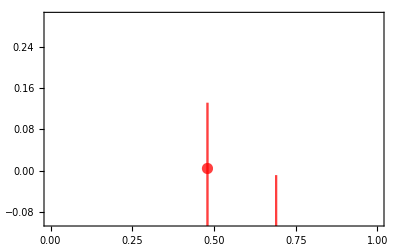

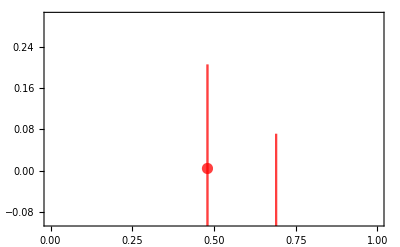

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

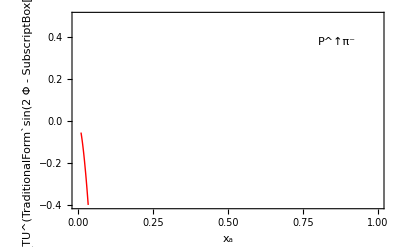

```mathematica
ATUsin2phiplot = Plot[ATUsin2phifuncIntegrated[x],{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.4,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑π^-",{0.85,0.85}]]
```

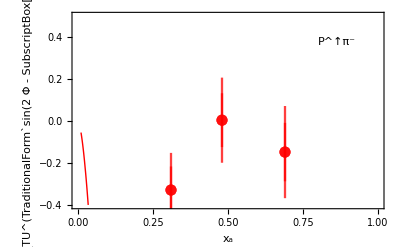

```mathematica
Show[ATUsin2phiplot, plotdataCOMPASSpim, plotdataCOMPASSpimsys]
```

```mathematica
Export["../tex/figs/ATUsin2phi_xpi.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_xpi.pdf

### Plot of xa = xN dependence

```mathematica
ATUsin2phifuncIntegrated[x_] :=ATUpionsin2phiIntegrated[x,0.5,25];
```

```mathematica
Clear[data,tab];
data=Cases[Import["./data/files_HEPDATA/A_T_sin_2phiCS_m_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

-Graphics-

```mathematica
ATUsin2phiplot = Plot[ATUsin2phifuncIntegrated[x],{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.4,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑π^-",{0.85,0.85}]]
```

-Graphics-

```mathematica
Show[ATUsin2phiplot, plotdataCOMPASSpim, plotdataCOMPASSpimsys]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phi_xN.pdf",%,Background->None]
```

../tex/figs/ATUsin2phi_xN.pdf

Phenomenology of leading twist single spin asymmetry A_TU^sin[2Φ+Φ_b]RHIC

## A_TU^sin[2Φ+Φ_b] analytical result:

```mathematica
Print["Eq(97)  C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ]"  ]
weightTUsin2phiplusphib[kt_,qT_,phi_] := 1/(2 MA^2 MB)(2kt Cos[phi](2 kt Cos[phi](qT-kt Cos[phi])-(kt Cos[phi]-kt^2))-kt^2(qT-kt Cos[phi]));
qTweightTUsin2phiplusphib[kt_] := 1;
```

Eq(97)  C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ]

```mathematica
Print["Eq(97)  F_TU^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ]"  ]
ConvolutionTMD[weightTUsin2phiplusphib,h1Tperpa,h1perpb]
```

Eq(97)  F_TU^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ]

-((2 ⅇ^(-q_T^2/(k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)) h_b^(FIRST perp) h_Ta^(perp SECOND) MA^2 MB (k_bTBOERMULDERS^2 (k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)^2-k_bTBOERMULDERS^2 (k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)^2 q_T+2 k_aTPRETZELOSITY^2 (k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2) q_T^2-k_aTPRETZELOSITY^2 (2 k_aTPRETZELOSITY^2+3 k_bTBOERMULDERS^2) q_T^3))/(k_aTPRETZELOSITY^2 k_bTBOERMULDERS^2 (k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)^4 π))

```mathematica
Print["Eq(97)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= ∫ⅆ^2q_T C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ] ="  ]
qTConvolutionTMD[qTweightTUsin2phiplusphib,weightTUsin2phiplusphib,h1Tperpa,h1perpb]
```

Eq(97)  ∫ⅆ^2q_TF_UT^(TraditionalForm`sin[2  Φ + SubscriptBox[Φ, b]])= ∫ⅆ^2q_T C[ (2 OverscriptBox[h, _] . SubscriptBox[k, aT][2 (OverscriptBox[h, _] . SubscriptBox[k, aT]) (OverscriptBox[h, _] . SubscriptBox[k, bT]) - (SubscriptBox[k, aT] . SubscriptBox[k, bT])] - SubsuperscriptBox[k, aT, 2] (OverscriptBox[h, _] . SubscriptBox[k, bT]))/(2 SubsuperscriptBox[M, a, 2] SubscriptBox[M, b])  h_(1  Ta)^⊥ OverBar[h_(1  b)^⊥] ] =

(h_b^(FIRST perp) h_Ta^(perp SECOND) MA^2 MB (-8 k_aTPRETZELOSITY^2 √(k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)-4 k_bTBOERMULDERS^2 √(k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)+(6 (k_aTPRETZELOSITY^2)^2+11 k_aTPRETZELOSITY^2 k_bTBOERMULDERS^2+2 (k_bTBOERMULDERS^2)^2) √π))/(2 k_aTPRETZELOSITY^2 k_bTBOERMULDERS^2 (k_aTPRETZELOSITY^2+k_bTBOERMULDERS^2)^(3/2))

## A_TU^sin[2Φ+Φ_a] numerics for A=proton, B=proton:

```mathematica
Ma = Mproton; (*proton*)
Mb = Mproton; (*proton*)
avkBMa = avkBM;
avkBMb = avkBM;
avkPa = avkBM;
avkPb = avkBM;


avTUsin2phiplusphibPT:= avkBMb+avkPa;

gTUsin2phiplusphib[qT_] := (2 Mp^4 (-avkBMb avTUsin2phiplusphibPT^2 + 3 avkPa avkBMb avTUsin2phiplusphibPT qT - 2 avkPa avTUsin2phiplusphibPT qT^2+ avkPa (avkBMb+2 avkPa) qT^3))/(π Ma^2 Mb avkBMb avTUsin2phiplusphibPT^4) Exp[(-qT^2/avTUsin2phiplusphibPT)]
aTUsin2phiplusphib := Mp^4  (-8 avkPa √avTUsin2phiplusphibPT-4 avkBMb √avTUsin2phiplusphibPT+3 avkPa (3 avkBMb+2 avkPa)√π)/( 2 Ma^2 Mb avkBMb √(avTUsin2phiplusphibPT^3))  

FTUsin2phiplusphib[xa_,xb_,Q2_,qT_] := ((4.0/9.0)h1TperpuFirstMoment[xa,Q2] h1perpubarFirstMoment[xb,Q2] +(1.0/9.0)h1TperpdFirstMoment[xa,Q2] h1perpdbarFirstMoment[xb,Q2]) gTUsin2phiplusphib[qT]


FTUsin2phiplusphibIntegrated[xa_,xb_,Q2_] := ((4.0/9.0)h1TperpuFirstMoment[xa,Q2] h1perpubarFirstMoment[xb,Q2] +(1.0/9.0)h1TperpdFirstMoment[xa,Q2] h1perpdbarFirstMoment[xb,Q2]) aTUsin2phiplusphib
```

```mathematica
Plot[{FTUsin2phiplusphib[0.1,0.3,1,PT],FUU1[0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_TU^sin[2Φ+Φ_a]numerics:

```mathematica
ATUsin2phiplusphib[xa_,xb_,Q2_,qT_] := FTUsin2phiplusphib[xa,xb, Q2,qT]/FUU1[xa,xb, Q2,qT];

ATUsin2phiplusphibIntegrated[xa_,xb_,Q2_] := FTUsin2phiplusphibIntegrated[xa,xb, Q2]/FUU1Integrated[xa,xb, Q2];
```

### Plot of qT dependence

```mathematica
ATUsin2phiplusphibfuncqT[qT_] :=ATUsin2phiplusphib[0.25,0.54,12.4, qT];
```

```mathematica
ATUsin2phiplusphibplotqT = Plot[{ATUsin2phiplusphibfuncqT[qT]},{qT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"q_T (GeV)","A_TU^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P^↑P"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Show[ATUsin2phiplusphibplotqT]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phiplusphib_qT.pdf",%,Background->None]
```

../tex/figs/ATUsin2phiplusphib_qT.pdf

### Plot of x dependence

```mathematica
ATUsin2phiplusphibfuncIntegrated[x_] :=ATUsin2phiplusphibIntegrated[x,0.54,12.4];
```

```mathematica
ATUsin2phiplusphibplot = Plot[{ATUsin2phiplusphibIntegrated[x,0.54,12.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x_a","A_TU^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed["P^↑P",{0.85,0.85}]]
```

-Graphics-

```mathematica
Show[ATUsin2phiplusphibplot]
```

-Graphics-

```mathematica
Export["../tex/figs/ATUsin2phiplusphib_x.pdf",%,Background->None]
```

../tex/figs/ATUsin2phiplusphib_x.pdf

```mathematica
l=Show[ColorData["SunsetColors","Image"],ImageSize->120,Frame->True,FrameTicks->{{None,None},{{{0,"Low"},{1,"High"}},None}}]
```

-Graphics-

```mathematica
DensityPlot[x+Sin[x y],{x,0,6},{y,-3,3},ColorFunction->"SunsetColors",FrameLabel->l]
```

-Graphics-

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2}]
```

-Graphics-